Symbolic integration of the cosine-weighted constant visibility function ∫cosθ sinθⅆθ= -1/2 cos^2 θ
Integration over the entire hemisphere ∫_0^(2π) ∫_0^(π/2) cosθ sinθⅆθⅆϕ=π

```mathematica
2π * Integrate[Cos[θ]Sin[θ],{θ,0,π/2}]
```

π

We can then assume that the Ambient Occlusion value of a flat, unoccluded surface should equal π, which is then scaled to 1 to be stored into a classical AO texture.
So let’s decide that an AO map’s value should be scaled by π when read by a shader, multiplied by ρ/πthe surface’s albedo to obtain a [0,1] ambient reflectance value, then multiplied by the irradiance perceived by the surface to finally obtain the reflected radiance in the outgoing direction ω_o:
	L(x,ω_o) = ρ/π (π AO)E(x)=ρ AO E(x)

We can write the “direct” irradiance estimate as:
	E_0(x)=∫_Ω^□ L_0 V_dir(ω_i)(n.ω_i)ⅆ ω_i
Where L_0=1 and V_dir(ω_i) represents the direct visibility function that equals 1 if the ray is unoccluded by the surface, 0 otherwise.
We notice that E_0(x) is exactly the value computed for the Ambient Occlusion, so E_0(x)=AO.

We can then write the general expression for the “indirect” irradiance estimate as:
	E_(n+1)(x)=∫_Ω^□ L_i(x,ω_i )V_ind(ω_i)(n.ω_i)ⅆ ω_i
Where V_ind(ω_i) represents the indirect visibility function that equals 1 if the ray is occluded by the surface, 0 otherwise (so V_ind(ω_i)=1-V_dir(ω_i) ).
We can rewrite the perceived incoming luminance L_i(x,ω_i ) from a neighbor location x' as:
	L_i(x,ω_i )=ρ/π E_n(x')
And finally:
	E_(n+1)(x)=∫_Ω^□ ρ/π E_n(x')V_ind(ω_i)(n.ω_i)ⅆ ω_i

We easily see that we can compute the irradiance incrementally by re-using the previous irradiance at the indirect neighbor locations.

## Fitting Experimental Data

After writing the program that computes the AO and the multiple indirect bounces from a height map, we collect the bounced illuminance values into histograms where the bin indices are given by the AO values: this bascially computes the average indirect illuminance perceived by a point given its AO value (AO value is in [0,π] but we rescaled it to [0,1] for convenience).
We do that for multiple bounces to try and find a pattern in the shape and amplitude of the curves...

To generate the curves shown below, we used the WallHeight.png as a height map, and its corresponding WallNormal.png as a normal map.
We also chose a height value of 5 cm for a total wall length of 1 meter, 1024 rays at 179° cone aperture.
It gave some nice curves without the annoying artefacts found at the extremas that can be found with other maps.

```mathematica
ClearAll["Global`*"]
```

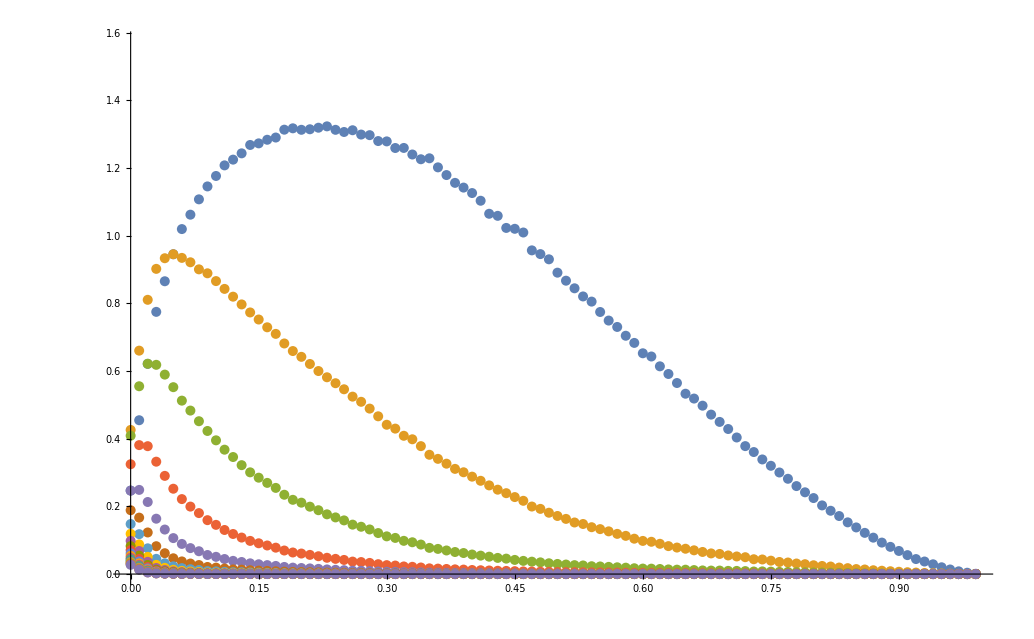

```mathematica
SetDirectory[NotebookDirectory[]]; 
tableSize = 100;
bouncesCount = 20;
rawArray=Table[ BinaryReadList["WallHeight"<>ToString[i]<>".float", "Real32"],{i,1,bouncesCount}];
bounces = Table[Table[{(i-1)/tableSize,rawArray[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];
ListPlot[bounces,PlotRange->{0,π/2}]
```

These were the original curves where I made the mistake of using initial direct illuminance E0 instead of AO to drive the histogram bins storage:

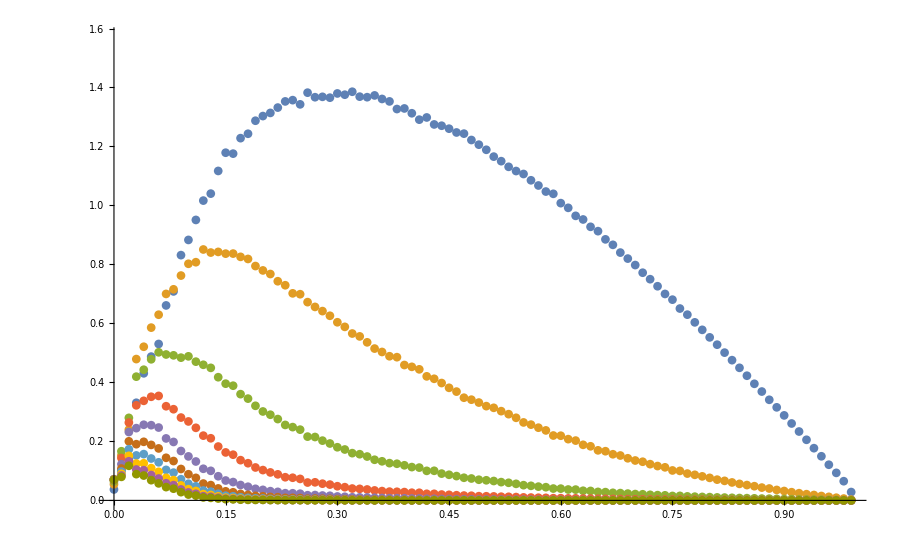

-Graphics-

## Starting the Fitting

Intuitively, it looks like a log-normal distribution curve that we can model as f(x)=a*x*(1-x)*e^-bx.
We can see below that it’s actually a very nice fit for the curves and may even deduce a general rule to find a and b coefficients as a function of the bounce index...

```mathematica
Manipulate[Plot[8*x*(1-x)*ⅇ^(-k*x),{x,0,1},PlotRange->{0,π/2}],{{k,1},0,20}]
```

```mathematica
Clear[a,b]
model=b/a*x*(1-x)*Exp[-b*x];
fitter[i_]:=Module[{},
FindFit[bounces[[i]], model,{a,{b,20}},{x}]
]
fits=Table[fitter[bounceIndex],{bounceIndex,1,bouncesCount}]
```

{{a→0.190288,b→3.14545},{a→0.343707,b→8.44232},{a→0.5864,b→16.9096},{a→1.00143,b→30.3989},{a→1.61136,b→50.1971},{a→2.39212,b→72.4272},{a→3.30553,b→91.7548},{a→4.322,b→106.562},{a→5.43418,b→117.492},{a→6.64514,b→125.656},{a→7.95951,b→131.97},{a→9.38098,b→137.06},{a→10.9125,b→141.323},{a→12.5566,b→145.006},{a→14.3163,b→148.263},{a→16.1946,b→151.189},{a→18.1951,b→153.851},{a→20.3215,b→156.291},{a→22.5784,b→158.539},{a→24.971,b→160.615}}

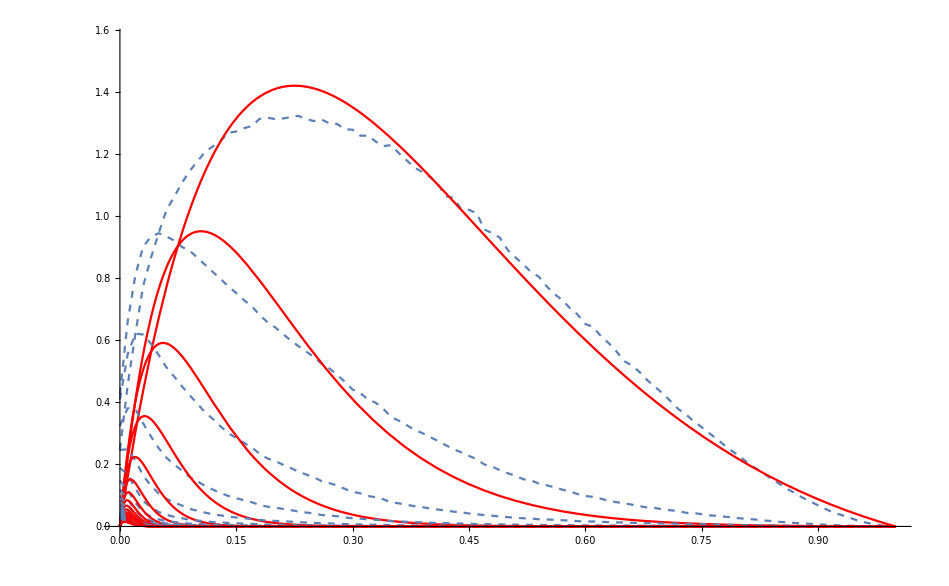

```mathematica
Show[
Table[{ListLinePlot[bounces[[bounceIndex]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[model/.fits[[bounceIndex]],{x,0,1},PlotRange->Full,PlotStyle->Red]},{bounceIndex,1,bouncesCount}]
]
```

Now we plot the various a and b coefficients as a function of the bounce index:

{0.190288,0.343707,0.5864,1.00143,1.61136,2.39212,3.30553,4.322,5.43418,6.64514,7.95951,9.38098,10.9125,12.5566,14.3163,16.1946,18.1951,20.3215,22.5784,24.971}

{3.14545,8.44232,16.9096,30.3989,50.1971,72.4272,91.7548,106.562,117.492,125.656,131.97,137.06,141.323,145.006,148.263,151.189,153.851,156.291,158.539,160.615}

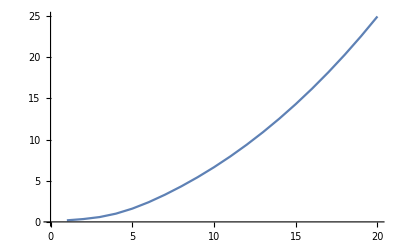

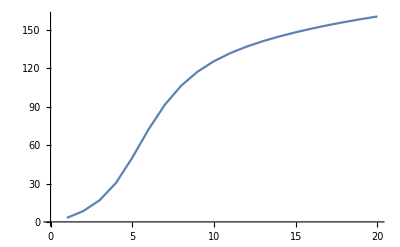

```mathematica
coeffsA=Table[a/.fits[[bounceIndex]],{bounceIndex,1,bouncesCount}]
coeffsB=Table[b/.fits[[bounceIndex]],{bounceIndex,1,bouncesCount}]
ListLinePlot[coeffsA,PlotRange->Full]
ListLinePlot[coeffsB,PlotRange->Full]
```

We notice the curves are almost linear so let’s try and fit the a and b coefficients as a linear function of the bounce index:

{a0→0.,a1→0.167151,a2→0.0599735}

FindFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{b0→1.,b1→1.,b2→1.,b3→1.}

Function[{x},3.14545+8.07737 (-1+x)]

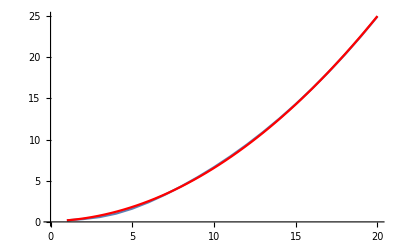

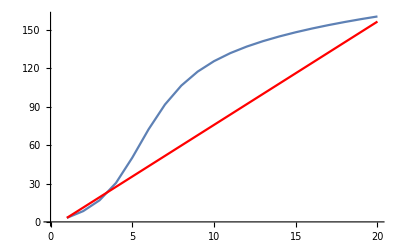

```mathematica
modelA=coeffsA[[1]]+0*a0+a1*(x-1)+a2*(x-1)^2;
modelB=coeffsB[[1]]+0*b0+b1*(x-1)+b2*(x-1)^2+b3*(x-1)^3;
modelB=coeffsB[[1]]+0*b0+b1*(x-1);
modelB=coeffsB[[1]]+(x-1)/(bouncesCount-1)*(coeffsB[[bouncesCount]] - coeffsB[[1]] - 4);
modelFitA=FindFit[coeffsA,modelA,{a0,a1,a2},{x}]
modelFitB=FindFit[coeffsB,modelB,{b0,b1,b2,b3},{x}]
(*Show[ListPlot[coeffsA,PlotRange->Full],Plot[modelA/.modelFitA,{x,0,bouncesCount}]]
Show[ListPlot[coeffsB,PlotRange->Full],Plot[modelB/.modelFitB,{x,0,bouncesCount}]]*)

modelFitA=Function[{x},Evaluate[modelA/.modelFitA]];
modelFitB=Function[{x},Evaluate[modelB/.modelFitB]]
Show[ListLinePlot[coeffsA,PlotRange->Full],Plot[modelFitA[x],{x,1,bouncesCount},PlotStyle->Red]]
Show[ListLinePlot[coeffsB,PlotRange->Full],Plot[modelFitB[x],{x,1,bouncesCount},PlotStyle->Red]]
```

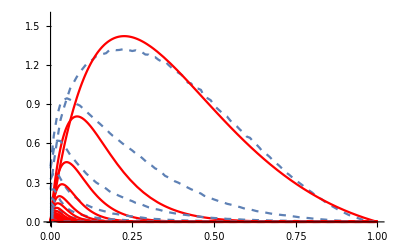

```mathematica
Show[
Table[{ListLinePlot[bounces[[bounceIndex]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[model/.{a-> modelFitA[bounceIndex],b-> modelFitB[bounceIndex]},{x,0,1},PlotRange->Full,PlotStyle->Red]},{bounceIndex,1,bouncesCount}]
]
```

{16.5299,24.5625,28.8363,30.3554,31.1519,30.2774,27.758,24.6557,21.6209,18.9095,16.5802,14.6104,12.9506,11.5482,10.3562,9.33576,8.45563,7.69091,7.02169,6.43208}

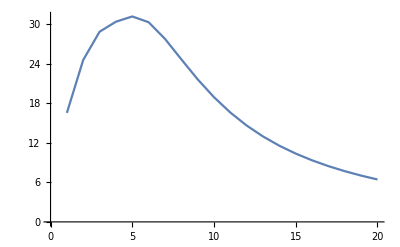

```mathematica
finalCoeffs=Table[coeffsB[[i]]/coeffsA[[i]],{i,1,bouncesCount}]
ListLinePlot[finalCoeffs]
```

## Refitting with Constrained b

Assuming b=?? we can try and re-fit the remaining variable a:

```mathematica
Clear[a,b]
fitter[i_]:=Module[{},
b = modelFitB[i];
FindFit[bounces[[i]], model,{a},{x}]
];
fits=Table[fitter[bounceIndex],{bounceIndex,1,bouncesCount}];
newCoeffsA=Table[a/.fits[[bounceIndex]],{bounceIndex,1,bouncesCount}]
Clear[a,b]
```

{0.190288,0.317818,0.557032,1.05144,1.93909,3.23565,4.77961,6.38134,7.95081,9.48118,10.9949,12.5144,14.0548,15.6233,17.2217,18.8481,20.4976,22.1639,23.8395,25.5167}

0.190288+1.33297 (-1+x)

0.190288+a0 (-1+x)+a1 (-1+x)^2

0.190288+a0 (-1+x)+a1 (-1+x)^2+a2 (-1+x)^3

{a0→0.0956329,a1→0.13019,a2→-0.00348261}

a0→0.0956329

a1→0.0650949

{a0→0.0956329,a1→0.0650949,a2→0.}

Function[{x},0.190288+0.0956329 (-1+x)+0.0650949 (-1+x)^2]

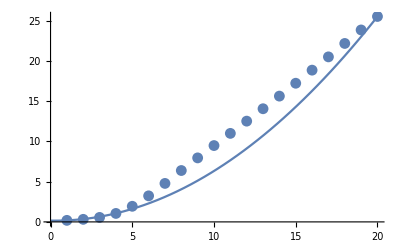

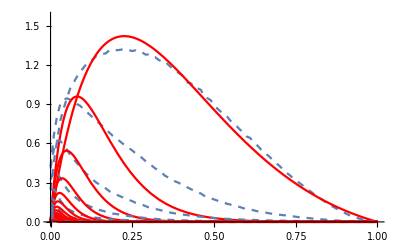

```mathematica
Clear[a0,a1,a2]
modelA=newCoeffsA[[1]]+(x-1)/(bouncesCount-1)*(newCoeffsA[[bouncesCount]]-newCoeffsA[[1]])
modelA=newCoeffsA[[1]]+a0*(x-1)+a1*(x-1)^2
modelA=newCoeffsA[[1]]+a0*(x-1)+a1*(x-1)^2+a2*(x-1)^3
modelFitA=FindFit[newCoeffsA,modelA,{a0,a1,a2},{x}]
modelFitA[[1]]=a0-> 1.0*(a0/.modelFitA[[1]])
modelFitA[[2]]=a1-> 0.5*(a1/.modelFitA[[2]])
modelFitA[[3]]=a2-> 0.0;
modelFitA
modelFitA=Function[{x},Evaluate[modelA/.modelFitA]]
Show[ListPlot[newCoeffsA,PlotRange->Full],Plot[modelFitA[x],{x,0,bouncesCount}]]
Clear[a,b]
Show[
Table[{ListLinePlot[bounces[[bounceIndex]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[model/.{ b-> modelFitB[bounceIndex],a->modelFitA[bounceIndex]},{x,0,1},PlotRange->Full,PlotStyle->Red]},{bounceIndex,1,bouncesCount}]
]
```

Reference graph without manual change of fitting variables (a0,a1,a2):

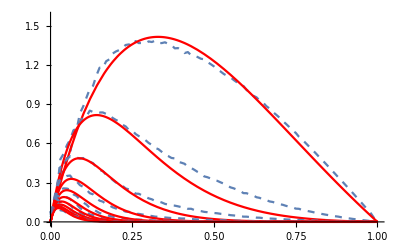

-Graphics-

## Using Fitted Data

Okay so we ended up with these expressions for a and b coefficients depending on i, the bounce index:
	a=0.145266+0.19848 (i-1)+0.024278 (i-1)^2
	b=1.55043+3.93698 (i-1)

We plug these into the reflectance model depending on α=AO/π:
	f(α,i)=b/a*α*(1-α)*ⅇ^(-b α)

As agreed, we assume the surface albedo ρ is constant in the surrounding of the luminance estimate and we can compute the final luminance due to indirect bounce on the surface as:

	L_indirect(x,ω_o) = 1/π[ρ AO(x) + ∑_(i=1)^N ρ^i f((AO(x))/π,i)]  E(x)

We notice the interesting property of albedo saturation as the amount of bounces increases.

## Verifying

We open the experimental ρ = 0.5 curves:

BinaryReadList::nffil: File not found during BinaryReadList["WallHeight11 - rho=0.5.float", "Real32"].

BinaryReadList::nffil: File not found during BinaryReadList["WallHeight12 - rho=0.5.float", "Real32"].

BinaryReadList::nffil: File not found during BinaryReadList["WallHeight13 - rho=0.5.float", "Real32"].

General::stop: Further output of BinaryReadList :: nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

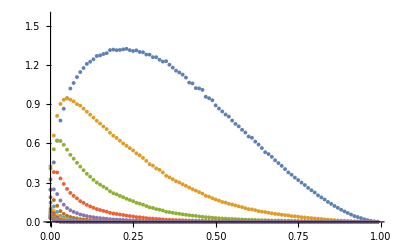

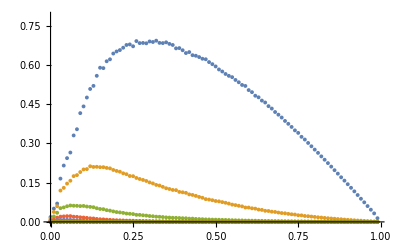

```mathematica
rawArray05=Table[ BinaryReadList["WallHeight"<>ToString[i]<>" - rho=0.5.float", "Real32"],{i,1,bouncesCount}];
bounces05 = Table[Table[{(i-1)/tableSize,rawArray05[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];
ListPlot[bounces,PlotRange->{0,π/2}]
ListPlot[bounces05,PlotRange->{0,π/4}]
```

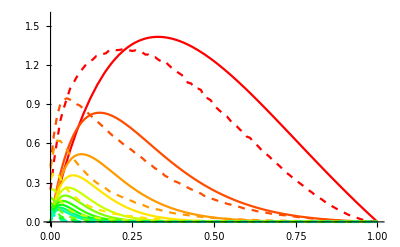

```mathematica
a[i_]:=0.14526642906187737+0.1984799936582921 (i-1)+0.024277999559107394 (i-1)^2
b[i_]:=1.5504282580946984+3.936979219376581 (i-1)
f[α_,i_]:=b[i]/a[i] α(1-α)ⅇ^(-b[i]α)
Show[Table[Plot[f[x,i],{x,0,1},PlotRange->{{0,1},{0,π/2}},PlotStyle->Hue[(i-1)/20]],{i,1,10}],
Table[ListLinePlot[bounces[[i]],PlotRange->Full,PlotStyle->{Dashed,Hue[(i-1)/20]}],{i,1,10}]]
```

And now for the moment of truth:

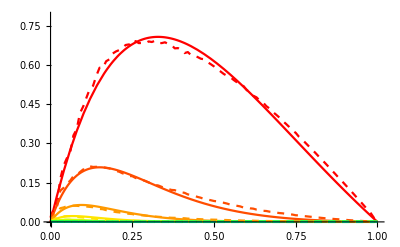

```mathematica
ρ=0.5;
Show[Table[Plot[ρ^i* f[x,i],{x,0,1},PlotRange->{{0,1},{0,π/4}},PlotStyle->Hue[(i-1)/20]],{i,1,10}],
Table[ListLinePlot[bounces05[[i]],PlotRange->Full,PlotStyle->{Dashed,Hue[(i-1)/20]}],{i,1,10}]]
```

## Let’s try and model a bounce function from its predecessor

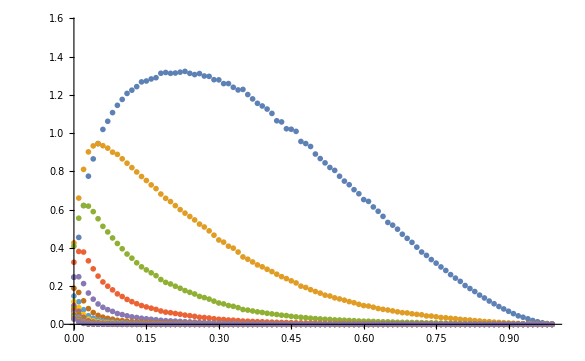

```mathematica
ListPlot[bounces,PlotRange->{0,π/2}]
```

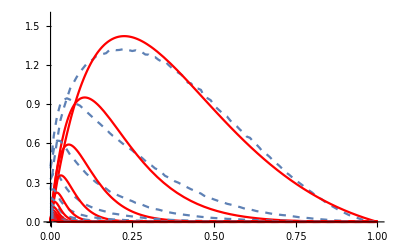

```mathematica
Clear[a,b]
model=b/a*x*(1-x)*Exp[-b*x];
fitter[i_]:=Module[{},
FindFit[bounces[[i]], model,{a,{b,20}},{x}]
]
fits=Table[fitter[bounceIndex],{bounceIndex,1,bouncesCount}];
Show[
Table[{ListLinePlot[bounces[[bounceIndex]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[model/.fits[[bounceIndex]],{x,0,1},PlotRange->Full,PlotStyle->Red]},{bounceIndex,1,bouncesCount}]
]
```

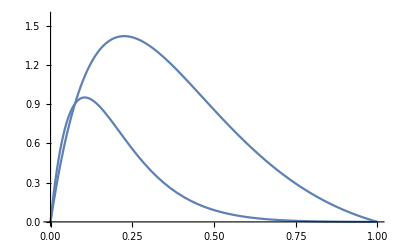

```mathematica
(* Build initial bounce function *)
f1=Function[{x},model/.fits[[1]]];
f2=Function[{x},model/.fits[[2]]];
Show[Plot[f1[x],{x,0,1},PlotRange->{0,π/2}],
Plot[f2[x],{x,0,1},PlotRange->{0,π/2}]]
(* Find how much f2 can be deduced from f1 by multiplying by an exponential *)
```

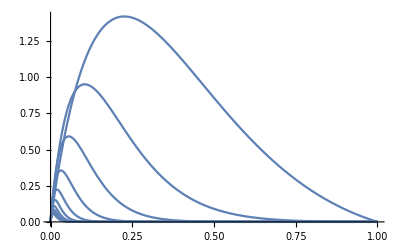

```mathematica
evals=Table[model/.fits[[bounceIndex]],{bounceIndex,1,bouncesCount}];
functor[i_]:=Module[{},
Function[{x},evals[[i]]]
]
funcs=Table[functor[bounceIndex],{bounceIndex,1,bouncesCount}];
Plot[funcs[[2]][x],{x,0,1}];
Show[Table[Plot[evals[[i]]/.x-> t,{t,0,1},PlotRange->All],{i,1,10}]];
Show[Table[Plot[funcs[[i]][x],{x,0,1},PlotRange->All],{i,1,10}]]
```

{a→1.48595,b→5.29687}

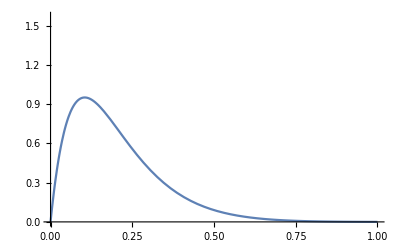

```mathematica
divModel=f1[x]*a*Exp[-b*x];
fit2=FindFit[bounces[[2]], divModel,{a,{b,20}},{x}]
fact2=Function[{x},divModel/.fit2];
Plot[fact2[x],{x,0,1},PlotRange->{0,π/2}]
```

{a→1.48595,b→5.29687}

{{a→1.48595,b→5.29687},{a→1.174,b→8.4673},{a→1.05268,b→13.4893},{a→1.02624,b→19.7982},{a→0.971928,b→22.2302},{a→0.916788,b→19.3276},{a→0.888237,b→14.807},{a→0.876914,b→10.9302},{a→0.874592,b→8.16413},{a→0.876818,b→6.31402},{a→0.881197,b→5.08979},{a→0.886394,b→4.26305},{a→0.891711,b→3.6832},{a→0.896786,b→3.25661},{a→0.901462,b→2.92656},{a→0.905724,b→2.66185},{a→0.909562,b→2.43993},{a→0.912986,b→2.2477},{a→0.91603,b→2.07661}}

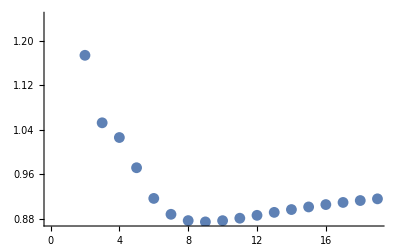

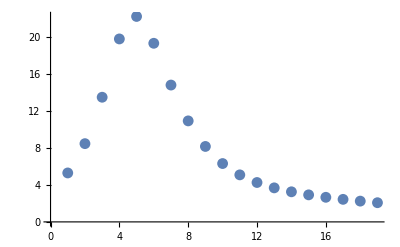

```mathematica
divModel=fprev*a*Exp[-b*x];
divFit=FindFit[bounces[[2]], divModel/.{fprev->f1[x]},{a,{b,1}},{x}]
divCoeffs=Table[FindFit[bounces[[bounceIndex]], divModel/.{fprev->funcs[[bounceIndex-1]][x]},{a,{b,20}},{x}],{bounceIndex,2,bouncesCount}]
ListPlot[a/.divCoeffs]
ListPlot[b/.divCoeffs]
```

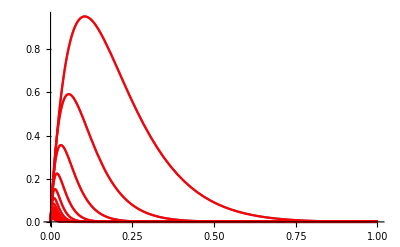

```mathematica
Show[
Table[Plot[funcs[[i]][x],{x,0,1},PlotRange->All],{i,2,bouncesCount}],
Table[Plot[funcs[[i-1]][x]*(a*Exp[-b*x]/.divCoeffs[[i-1]]),{x,0,1},PlotStyle->Red,PlotRange->All],{i,2,bouncesCount}]
]
```

Let’s fix b to a constant so we’re left with multiplying by a constant exponential value and coefficient a:

4.38

4.

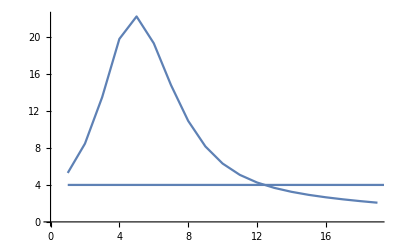

```mathematica
Clear[h]
defB = h/.FindFit[b/.divCoeffs,h,{h},{x}];
defB = 4.38
defB = 4.0
Show[ListLinePlot[b/.divCoeffs,PlotRange->All],Plot[defB,{x,1,bouncesCount},PlotRange->All]]
```

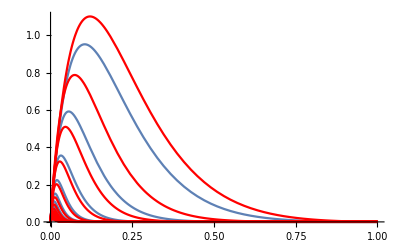

```mathematica
Show[
Table[Plot[funcs[[i]][x],{x,0,1},PlotRange->All],{i,2,bouncesCount}],
Table[Plot[funcs[[i-1]][x]*(a*Exp[-defB*x]/.divCoeffs[[i-1]]),{x,0,1},PlotStyle->Red,PlotRange->All],{i,2,bouncesCount}]
]
```

We see that now the amplitude coefficients a are a bit off so we need to recompute them with fixed factor b:

{{a→0.83794},{a→1.32688},{a→1.66742},{a→1.74199},{a→1.61575},{a→1.45484},{a→1.33662},{a→1.25986},{a→1.20968},{a→1.17535},{a→1.15059},{a→1.13185},{a→1.11711},{a→1.10515},{a→1.0952},{a→1.08677},{a→1.07951},{a→1.0732},{a→1.06765}}

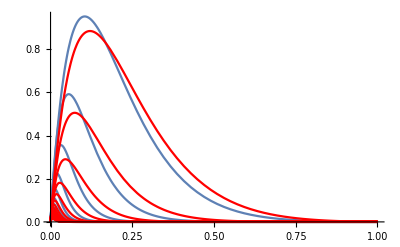

```mathematica
divModel=fprev*1/a*Exp[-defB*x];
divCoeffsA=Table[FindFit[bounces[[bounceIndex]], divModel/.{fprev->funcs[[bounceIndex-1]][x]},{a},{x}],{bounceIndex,2,bouncesCount}]
Show[
Table[Plot[funcs[[i]][x],{x,0,1},PlotRange->All],{i,2,bouncesCount}],
Table[Plot[funcs[[i-1]][x]*(1/a*Exp[-defB*x]/.divCoeffsA[[i-1]]),{x,0,1},PlotStyle->Red,PlotRange->All],{i,2,bouncesCount}]
]
```

FindFit::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the norm of the residual. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{a→0.979499,b→0.958615,c→0.215839}

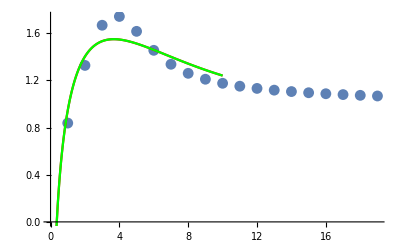

```mathematica
logModel=a;
logModel=a+Log[b*x]*Exp[-c*x];
logFit=FindFit[a/.divCoeffsA,logModel,{{a,1},{b,1,0.1,10},{c,1}},{x}]
glamour=Function[{x},logModel/.logFit];
Show[
ListPlot[a/.divCoeffsA,PlotRange->All],
Plot[logModel/.logFit,{x,0,10},PlotRange->All,PlotStyle->Red],
Plot[glamour[x],{x,0,10},PlotRange->All,PlotStyle->Green]
]
```

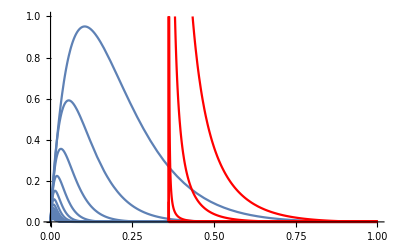

```mathematica
Show[
Table[Plot[funcs[[i]][x],{x,0,1},PlotRange->All],{i,2,bouncesCount}],
Table[Plot[funcs[[i-1]][x]*(Exp[-defB*x]/glamour[i-1]),{x,0,1},PlotStyle->Red,PlotRange->{{0,10},{0,1}}],{i,2,bouncesCount}]
]
```

## Shifting Perspective

What if we tried to use the initial f1 curve’s coefficient over itself multiple times, as we’ll certainly do it in code?
That requires shifting the curves on themselves:

```mathematica
ta=Table[ funcs[[i]][1]/.x-> 0.5,{i,1,bouncesCount}];
ListLinePlot[ta,PlotRange->{{0,10},{0,π/2}}];
```

```mathematica
Manipulate[ListLinePlot[Table[ funcs[[i]][1]/.x-> t ,{i,1,bouncesCount}],PlotRange->{{1,10},{0,π/2}}],{{t,0.5},0,1}]
```

```mathematica
bouncesCount=8;
ta3D=Table[Table[ funcs[[i]][1]/.x-> t/100,{i,1,bouncesCount}],{t,0,100}];
ta3D=Table[Table[ (funcs[[i]][1]/.x-> t/100)/(t/100*(1-t/100)),{i,1,bouncesCount}],{t,10,99}];
ListPlot3D[ta3D,PlotRange->All,AxesLabel->{"Bounce Index","100*AO","Normalized Irradiance"}]
```

-Graphics3D-

Intuively, removing the α(1-α) shows us some sort of regular exponential decay whose decay rate is correlated to α as well...
Let’s try and see if that’s also the case with the original curves:

```mathematica
ta3D=Table[ Table[bounces[[i]][[j]][[2]],{j,1,100}],{i,1,bouncesCount}];
ta3D=Table[Table[ (bounces[[i]][[j]][[2]])/Max[0.01,(j-1)/99*(1-(j-1)/99)],{i,1,bouncesCount}],{j,1,100}];
MatrixForm[ta3D];
ListPlot3D[ta3D,PlotRange->All,AxesLabel->{"Bounces","α","Amplitude"}]
```

-Graphics3D-

Let’s try and fit the initial bounce value with an exponential:

{{1/11,13.8627},{19/99,8.49473},{29/99,6.17889},{13/33,4.78409},{49/99,3.72141},{59/99,2.83722},{23/33,2.12914},{79/99,1.49895},{89/99,0.885401}}

{a→18.8435,b→-67.3838,c→98.3834,d→-51.0819}

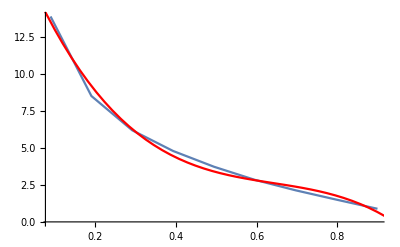

```mathematica
Clear[α,x]
modelA0=9.239635202619764*Exp[-b*(α-1)];
modelA0=a*Exp[-b*α];
modelA0=a+b*α+c*α^2+d*α^3;
samplesCount=Length[ta3D];
coeffsA0=Table[{(i-1)/(samplesCount-1),ta3D[[i]][[1]]},{i,10,90,10}]
fitA0=FindFit[coeffsA0,modelA0,{a,b,c,d},{α}]
fA0=Function[{α},modelA0/.fitA0];
Show[
ListLinePlot[coeffsA0,PlotRange->All],
Plot[fA0[α],{α,0,1},PlotRange->All,PlotStyle->Red]
]
```

Now let’s find a rule to drive the decay factor as a function of α :

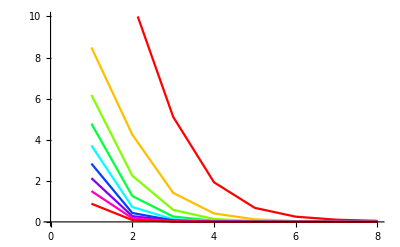

```mathematica
ta3Dortho=Transpose@ta3D;
Show[Table[ListLinePlot[ta3D[[sampleIndex]],PlotRange->{0,10},PlotStyle->Hue[(sampleIndex-10)/80]],{sampleIndex,10,90,10}]]
```

{6.17889,2.25106,0.585096,0.140971,0.0367348,0.0109489,0.00374367,0.00146051}

6.10364

6.10364 ⅇ^(-b (-1+x))

{a→1.,b→1.06452}

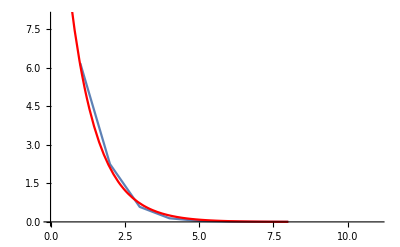

```mathematica
α=0.3;
sampleIndex=Round[α*samplesCount];
ta3D[[sampleIndex]]
A0=fA0[α]
modelDecay=A0*Exp[-b*(x-1)];
modelDecay=fA0[α]*Exp[-b*(x-1)]
fitDecay=FindFit[ta3D[[sampleIndex]],modelDecay,{a,b},{x}]
fDecay=Function[{x},modelDecay/.fitDecay];
Show[
ListLinePlot[ta3D[[sampleIndex]],PlotRange->{{0,11},{0,bouncesCount}}],
Plot[modelDecay/.fitDecay/.x-> bounceIndex,{bounceIndex,0,bouncesCount},PlotRange->Full,PlotStyle->Red]
]
```

Applying to many samples, we get a list of coefficients depending on α

{{x→0.1,a→13.0379,b→0.495213},{x→0.15,a→10.7771,b→0.690819},{x→0.2,a→8.89341,b→0.845452},{x→0.25,a→7.34835,b→0.954335},{x→0.3,a→6.10364,b→1.06452},{x→0.35,a→5.12099,b→1.17076},{x→0.4,a→4.36207,b→1.28326},{x→0.45,a→3.78858,b→1.39391},{x→0.5,a→3.3622,b→1.54939},{x→0.55,a→3.04463,b→1.70088},{x→0.6,a→2.79755,b→1.85994},{x→0.65,a→2.58265,b→2.01062},{x→0.7,a→2.36161,b→2.11386},{x→0.75,a→2.09614,b→2.20088},{x→0.8,a→1.74791,b→2.25238},{x→0.85,a→1.27861,b→2.22679},{x→0.9,a→0.64994,b→1.94888}}

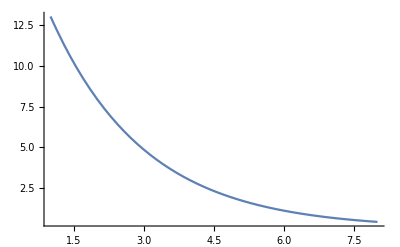

```mathematica
Clear[a,b]
fitter[α_]:=Module[{},
sampleIndex=Round[α*samplesCount];
A0=fA0[α];
modelDecay=A0*Exp[-b*(x-1)];
{x->α,a-> A0, FindFit[ta3D[[sampleIndex]],modelDecay,{b},{x}][[1]]}
]
fitsDecay=Table[fitter[α],{α,0.1,0.9,0.05}]
Plot[a*Exp[-b*(x-1)]/.fitsDecay[[1]],{x,1,bouncesCount},PlotRange->Full]
```

{{0.1,0.495213},{0.15,0.690819},{0.2,0.845452},{0.25,0.954335},{0.3,1.06452},{0.35,1.17076},{0.4,1.28326},{0.45,1.39391},{0.5,1.54939},{0.55,1.70088},{0.6,1.85994},{0.65,2.01062},{0.7,2.11386},{0.75,2.20088},{0.8,2.25238},{0.85,2.22679},{0.9,1.94888}}

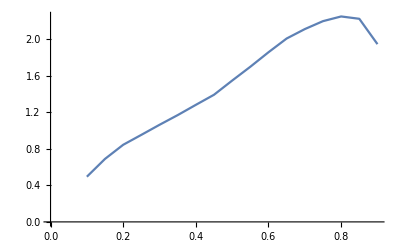

```mathematica
coeffsDecay={x,b}/.fitsDecay
ListLinePlot[coeffsDecay]
```

It looks a lot (!!) like a linear fit! <3

{a→0.406762,b→2.21729}

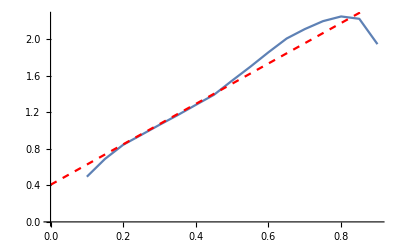

```mathematica
Clear[a,b,α]
modelCoeffsDecay=a+b*α;
fitCoeffsDecay=FindFit[coeffsDecay,modelCoeffsDecay,{a,b},{α}]
Show[
ListLinePlot[coeffsDecay],
Plot[modelCoeffsDecay/.fitCoeffsDecay,{α,0,1},PlotStyle->{Red,Dashed}]
]
```

## Putting it all together!

Okay so now it looks like we have it all: each curve for each bounce i is of the form f_i(α)=A_i*α*(1-α)*e^-B_iα as stated at the beginning of the document.
We later tried to shift our perspective to see, for a given α=AO/π, the shape of the curve we get for each new bounce and it looks like a simple exponential g(α,i)=A(α)ⅇ^(-B(α)i) with an initial amplitude A(α) and a decay factor B(α).
A very good fit for A(α)=12.255-26.1448α+27.5502 α^2-10.4155 α^3 that allows us to find a very simple linear fit for B(α)=0.186195+2.23562α

```mathematica
Clear[A,B]
A[α_]:=12.255-26.144751371564944α+27.5502 α^2-10.4155 α^3
B[α_]:=0.18619452933736622+2.235617876545042α
```

```mathematica
Manipulate[Plot[A[α]*Exp[-B[α]*x],{x,1,10},PlotRange->{0,10}],{{α,0},0,1}]
```

Let’s verify the curves fit our experimental data:

```mathematica
Manipulate[
Show[
ListLinePlot[ta3D[[Round[1+100*α]]],PlotRange->{0,10}],
Plot[A[α]*Exp[-B[α]*(x-1)],{x,1,10},PlotRange->{0,10},PlotStyle->Red]
],{{α,0.2},0,1}]
```

Now, we re-plot the entire data and final curves, with the attenuation curve:

```mathematica
(*finalTable3D=Table[Table[ (bounces[[i]][[j]][[2]])/Max[0.01,(j-1)/99*(1-(j-1)/99)],{i,1,bouncesCount}],{j,1,100}];*)
finalTable3D=Table[Table[ bounces[[i]][[j]][[2]],{i,1,bouncesCount}],{j,1,100}];
reconstructedTable3D=Table[Table[ α*(1-α)*A[α]*Exp[-B[α]*(i-1)],{i,1,bouncesCount}],{α,0,1,0.01}];
Show[ListPlot3D[finalTable3D,PlotRange->{0,π/2},AxesLabel->{"Bounces","α","Amplitude"}],
ListPlot3D[reconstructedTable3D,PlotRange->{0,π/2},AxesLabel->{"Bounces","α","Amplitude"},PlotStyle->Red]]
```

-Graphics3D-

So basically, in the shader, all we need to do is computing α=AO/π A_0=α(1-α)A(α) and K=ρ.ⅇ^(-B(α)) then the final expression for outgoing luminance is given by:

	 L(x,ω_o)=(ρ/π.AO +A_0/π ∑_(i=1)^∞ K^i )E(x)=(ρ/π.AO +A_0/π K/(1-K) )E(x)  since K<1

```mathematica
Manipulate[
A0=A[α];
K0=Exp[-B[α]];
Show[
ListPlot[Table[α*(1-α)*A0*Product[K0,{i,maxI}],{maxI,1,bouncesCount}],PlotRange->{0,π/4}],
Plot[α*(1-α)*A0*Exp[-B[α]*x],{x,1,10},PlotRange->All,PlotStyle->Red]
],{{α,0.1},0,1}]
```

Final verification with the 50% albedo table:

```mathematica
ρ=0.5;
finalTable3D=Table[Table[ bounces05[[i]][[j]][[2]],{i,1,bouncesCount}],{j,1,100}];
reconstructedTable3D=Table[Table[ α*(1-α)*A[α]*ρ^i*Exp[-B[α]*(i-1)],{i,1,bouncesCount}],{α,0,1,0.01}];
Show[ListPlot3D[finalTable3D,PlotRange->{0,π/4},AxesLabel->{"Bounces","α","Amplitude"}],
ListPlot3D[reconstructedTable3D,AxesLabel->{"Bounces","α","Amplitude"},PlotStyle->Red]]
```

-Graphics3D-

```mathematica
Clear[ρ,b]
ρ=0.5;
b=0.2;
K0=ρ*ⅇ^-b;
Sum[K0^x,{x,1,∞}]
K0/(1-K0)
```

0.693094

0.693094

```mathematica
ρ=1.0;
(*linearTable=Table[(i-1)/tableSize,{i,1,tableSize}];
sumTable=Sum[1/π ρ^i*bounces[[i]],{i,1,bouncesCount}];
finalTable=Table[{(i-1)/tableSize,(i-1)/tableSize+sumTable[[i]][[2]]},{i,1,tableSize}];*)
Manipulate[
sumTable=ρ*bounces[[1]]+(ρ/π)^2*bounces[[2]]+(ρ/π)^3*bounces[[3]]+(ρ/π)^4*bounces[[4]]+ρ^5*bounces[[5]]+ρ^6*bounces[[6]]+ρ^7*bounces[[7]];
sumTable=Sum[(ρ/1)^i*bounces[[i]],{i,1,bouncesCount}];
finalTable=Table[{(i-1)/tableSize,(i-1)/tableSize+1/π sumTable[[i]][[2]]},{i,1,tableSize}];
ListLinePlot[finalTable,PlotRange->{0,1.1}],{{ρ,0.1},0,1}]
```

Building the final expression to obtain the same kind of curve as the one in Jimenez’s paper:

```mathematica
Manipulate[Plot[α+1/π α*(1-α)*A[α]*(ρ*Exp[-B[α]])/(1-ρ*Exp[-B[α]]),{α,0,1},PlotRange->{0,1},PlotStyle->Red],{{ρ,0.1},0,1}]
```

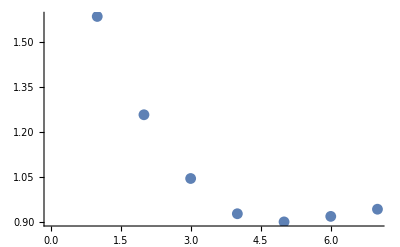

```mathematica
ListPlot[Table[(a/.divCoeffsA[[i]])/(a/.divCoeffsA[[i-1]]),{i,2,bouncesCount}]]
```

FindFit::ivar: 0.2 is not a valid variable.

FindFit[{{0,0.425977},{1/100,0.660285},{1/50,0.810531},{3/100,0.902011},{1/25,0.933438},{1/20,0.945136},{3/50,0.934449},{7/100,0.921476},{2/25,0.900596},{9/100,0.888919},{1/10,0.865887},{11/100,0.842813},{3/25,0.819797},{13/100,0.796926},{7/50,0.773194},{3/20,0.752314},{4/25,0.729294},{17/100,0.709858},{9/50,0.681496},{19/100,0.659109},{1/5,0.642013},{21/100,0.620873},{11/50,0.600027},{23/100,0.581623},{6/25,0.56403},{1/4,0.546134},{13/50,0.524349},{27/100,0.50911},{7/25,0.489011},{29/100,0.466244},{3/10,0.441255},{31/100,0.429854},{8/25,0.408663},{33/100,0.398343},{17/50,0.378073},{7/20,0.352553},{9/25,0.340482},{37/100,0.326232},{19/50,0.310845},{39/100,0.300846},{2/5,0.287878},{41/100,0.275639},{21/50,0.262022},{43/100,0.249399},{11/25,0.239041},{9/20,0.227531},{23/50,0.2165},{47/100,0.199562},{12/25,0.192676},{49/100,0.18127},{1/2,0.171668},{51/100,0.163028},{13/25,0.15243},{53/100,0.147936},{27/50,0.138472},{11/20,0.132807},{14/25,0.126227},{57/100,0.118765},{29/50,0.112923},{59/100,0.104525},{3/5,0.0979519},{61/100,0.0954029},{31/50,0.0894231},{63/100,0.082577},{16/25,0.0783112},{13/20,0.0748249},{33/50,0.0701587},{67/100,0.0653131},{17/25,0.0610211},{69/100,0.059434},{7/10,0.0549731},{71/100,0.0519994},{18/25,0.049824},{73/100,0.0438096},{37/50,0.0430787},{3/4,0.0395766},{19/25,0.0357034},{77/100,0.0341387},{39/50,0.0311613},{79/100,0.0291523},{4/5,0.0260195},{81/100,0.0239228},{41/50,0.0222615},{83/100,0.019242},{21/25,0.0174605},{17/20,0.0147428},{43/50,0.0134814},{87/100,0.0112534},{22/25,0.00982036},{89/100,0.00833437},{9/10,0.00678361},{91/100,0.00544286},{23/25,0.00437493},{93/100,0.00330638},{47/50,0.00240838},{19/20,0.00172409},{24/25,0.00116084},{97/100,0.000666433},{49/50,0.000266133},{99/100,0.0000422741}},(3.30598 ⅇ^(-0.4 x) (1-x) x)/a,{a,0.2},{x}]

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.425977}, {1/100, 0.660285}, {1/50, 0.810531}, {3/100, 0.902011}, {1/25, 0.933438}, {1/20, 0.945136}, {3/50, 0.934449}, {7/100, 0.921476}, {2/25, 0.900596}, {9/100, 0.888919}, {1/10, 0.865887}, {11/100, 0.842813}, {3/25, 0.819797}, « 26 », {39/100, 0.300846}, {2/5, 0.287878}, {41/100, 0.275639}, {21/50, 0.262022}, {43/100, 0.249399}, {11/25, 0.239041}, {9/20, 0.227531}, {23/50, 0.2165}, {47/100, 0.199562}, {12/25, 0.192676}, {49/100, 0.18127}, « 50 »}, « 22 »/a, {a, 0.2}, {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0.425977}, {1/100, 0.660285}, {1/50, 0.810531}, {3/100, 0.902011}, {1/25, 0.933438}, {1/20, 0.945136}, {3/50, 0.934449}, {7/100, 0.921476}, {2/25, 0.900596}, {9/100, 0.888919}, {1/10, 0.865887}, {11/100, 0.842813}, {3/25, 0.819797}, « 26 », {39/100, 0.300846}, {2/5, 0.287878}, {41/100, 0.275639}, {21/50, 0.262022}, {43/100, 0.249399}, {11/25, 0.239041}, {9/20, 0.227531}, {23/50, 0.2165}, {47/100, 0.199562}, {12/25, 0.192676}, {49/100, 0.18127}, « 50 »}, « 2 », {0.0204286}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

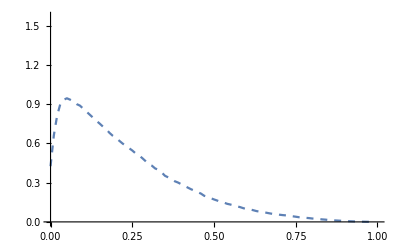

```mathematica
f1=Function[{x},model/.fits[[1]]];
Plot[f1[x],{x,0,1}];
model2=f1[x]*b/a*Exp[-b*x];
fit2=FindFit[bounces[[2]],model2,{a,b},{x}]
f2=Function[{x},model2/.fit2];
Show[
ListLinePlot[bounces[[2]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[f2[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.425977}, {1/100, 0.660285}, {1/50, 0.810531}, {3/100, 0.902011}, {1/25, 0.933438}, {1/20, 0.945136}, {3/50, 0.934449}, {7/100, 0.921476}, {2/25, 0.900596}, {9/100, 0.888919}, {1/10, 0.865887}, {11/100, 0.842813}, {3/25, 0.819797}, « 26 », {39/100, 0.300846}, {2/5, 0.287878}, {41/100, 0.275639}, {21/50, 0.262022}, {43/100, 0.249399}, {11/25, 0.239041}, {9/20, 0.227531}, {23/50, 0.2165}, {47/100, 0.199562}, {12/25, 0.192676}, {49/100, 0.18127}, « 50 »}, « 1 »/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

FindFit[{{0,0.408861},{1/100,0.555072},{1/50,0.621534},{3/100,0.618379},{1/25,0.589468},{1/20,0.552344},{3/50,0.512544},{7/100,0.483144},{2/25,0.45174},{9/100,0.422908},{1/10,0.395255},{11/100,0.367594},{3/25,0.345897},{13/100,0.32186},{7/50,0.300651},{3/20,0.284818},{4/25,0.269466},{17/100,0.254672},{9/50,0.234383},{19/100,0.219399},{1/5,0.211001},{21/100,0.199129},{11/50,0.188686},{23/100,0.176538},{6/25,0.167435},{1/4,0.158596},{13/50,0.146056},{27/100,0.139802},{7/25,0.131828},{29/100,0.121186},{3/10,0.111458},{31/100,0.106821},{8/25,0.0981738},{33/100,0.0939639},{17/50,0.0871555},{7/20,0.0773917},{9/25,0.0743363},{37/100,0.069698},{19/50,0.0651416},{39/100,0.0621454},{2/5,0.0577109},{41/100,0.0544547},{21/50,0.0513253},{43/100,0.0477255},{11/25,0.0455821},{9/20,0.0418072},{23/50,0.0389438},{47/100,0.0365992},{12/25,0.0345651},{49/100,0.0318595},{1/2,0.0298814},{51/100,0.0281237},{13/25,0.0263435},{53/100,0.0254139},{27/50,0.0231685},{11/20,0.0224386},{14/25,0.0212264},{57/100,0.0200166},{29/50,0.0188523},{59/100,0.0171664},{3/5,0.016184},{61/100,0.0159498},{31/50,0.0149609},{63/100,0.0136727},{16/25,0.0129881},{13/20,0.0128995},{33/50,0.0117642},{67/100,0.0107224},{17/25,0.0102654},{69/100,0.0103059},{7/10,0.0093958},{71/100,0.00931726},{18/25,0.00875938},{73/100,0.00755142},{37/50,0.00786916},{3/4,0.007178},{19/25,0.00633312},{77/100,0.00613219},{39/50,0.00551879},{79/100,0.00522356},{4/5,0.0045978},{81/100,0.00426884},{41/50,0.0039835},{83/100,0.00342179},{21/25,0.00308476},{17/20,0.00248955},{43/50,0.00234772},{87/100,0.00194671},{22/25,0.00168918},{89/100,0.00141607},{9/10,0.00115016},{91/100,0.000937474},{23/25,0.000738272},{93/100,0.0005532},{47/50,0.000408015},{19/20,0.000307784},{24/25,0.000206436},{97/100,0.000116264},{49/50,0.0000464428},{99/100,6.46993×10^-6}},1/a 0.2 ⅇ^(-0.2 x) ((3.30598 ⅇ^(-0.4 x) (1-x) x)/a/.FindFit[{{0,0.425977},{1/100,0.660285},{1/50,0.810531},{3/100,0.902011},{1/25,0.933438},{1/20,0.945136},{3/50,0.934449},{7/100,0.921476},{2/25,0.900596},{9/100,0.888919},{1/10,0.865887},{11/100,0.842813},{3/25,0.819797},{13/100,0.796926},{7/50,0.773194},{3/20,0.752314},{4/25,0.729294},{17/100,0.709858},{9/50,0.681496},{19/100,0.659109},{1/5,0.642013},{21/100,0.620873},{11/50,0.600027},{23/100,0.581623},{6/25,0.56403},{1/4,0.546134},{13/50,0.524349},{27/100,0.50911},{7/25,0.489011},{29/100,0.466244},{3/10,0.441255},{31/100,0.429854},{8/25,0.408663},{33/100,0.398343},{17/50,0.378073},{7/20,0.352553},{9/25,0.340482},{37/100,0.326232},{19/50,0.310845},{39/100,0.300846},{2/5,0.287878},{41/100,0.275639},{21/50,0.262022},{43/100,0.249399},{11/25,0.239041},{9/20,0.227531},{23/50,0.2165},{47/100,0.199562},{12/25,0.192676},{49/100,0.18127},{1/2,0.171668},{51/100,0.163028},{13/25,0.15243},{53/100,0.147936},{27/50,0.138472},{11/20,0.132807},{14/25,0.126227},{57/100,0.118765},{29/50,0.112923},{59/100,0.104525},{3/5,0.0979519},{61/100,0.0954029},{31/50,0.0894231},{63/100,0.082577},{16/25,0.0783112},{13/20,0.0748249},{33/50,0.0701587},{67/100,0.0653131},{17/25,0.0610211},{69/100,0.059434},{7/10,0.0549731},{71/100,0.0519994},{18/25,0.049824},{73/100,0.0438096},{37/50,0.0430787},{3/4,0.0395766},{19/25,0.0357034},{77/100,0.0341387},{39/50,0.0311613},{79/100,0.0291523},{4/5,0.0260195},{81/100,0.0239228},{41/50,0.0222615},{83/100,0.019242},{21/25,0.0174605},{17/20,0.0147428},{43/50,0.0134814},{87/100,0.0112534},{22/25,0.00982036},{89/100,0.00833437},{9/10,0.00678361},{91/100,0.00544286},{23/25,0.00437493},{93/100,0.00330638},{47/50,0.00240838},{19/20,0.00172409},{24/25,0.00116084},{97/100,0.000666433},{49/50,0.000266133},{99/100,0.0000422741}},(3.30598 ⅇ^(-0.4 x) (1-x) x)/a,{a,0.2},{x}]),{a,0.2},{x}]

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.425977}, {1/100, 0.660285}, {1/50, 0.810531}, {3/100, 0.902011}, {1/25, 0.933438}, {1/20, 0.945136}, {3/50, 0.934449}, {7/100, 0.921476}, {2/25, 0.900596}, {9/100, 0.888919}, {1/10, 0.865887}, {11/100, 0.842813}, {3/25, 0.819797}, « 26 », {39/100, 0.300846}, {2/5, 0.287878}, {41/100, 0.275639}, {21/50, 0.262022}, {43/100, 0.249399}, {11/25, 0.239041}, {9/20, 0.227531}, {23/50, 0.2165}, {47/100, 0.199562}, {12/25, 0.192676}, {49/100, 0.18127}, « 50 »}, « 22 »/a, {a, 0.2}, {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.425977}, {1/100, 0.660285}, {1/50, 0.810531}, {3/100, 0.902011}, {1/25, 0.933438}, {1/20, 0.945136}, {3/50, 0.934449}, {7/100, 0.921476}, {2/25, 0.900596}, {9/100, 0.888919}, {1/10, 0.865887}, {11/100, 0.842813}, {3/25, 0.819797}, « 26 », {39/100, 0.300846}, {2/5, 0.287878}, {41/100, 0.275639}, {21/50, 0.262022}, {43/100, 0.249399}, {11/25, 0.239041}, {9/20, 0.227531}, {23/50, 0.2165}, {47/100, 0.199562}, {12/25, 0.192676}, {49/100, 0.18127}, « 50 »}, « 22 »/a, {a, 0.2}, {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0.408861}, {1/100, 0.555072}, {1/50, 0.621534}, {3/100, 0.618379}, {1/25, 0.589468}, {1/20, 0.552344}, {3/50, 0.512544}, {7/100, 0.483144}, {2/25, 0.45174}, {9/100, 0.422908}, {1/10, 0.395255}, {11/100, 0.367594}, {3/25, 0.345897}, « 26 », {39/100, 0.0621454}, {2/5, 0.0577109}, {41/100, 0.0544547}, {21/50, 0.0513253}, {43/100, 0.0477255}, {11/25, 0.0455821}, {9/20, 0.0418072}, {23/50, 0.0389438}, {47/100, 0.0365992}, {12/25, 0.0345651}, {49/100, 0.0318595}, « 50 »}, « 1 »/a, « 1 », {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

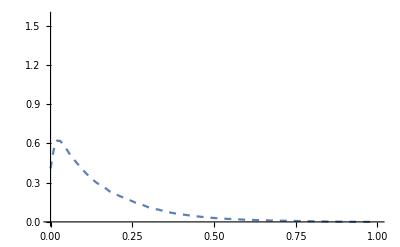

```mathematica
model3=f2[x]*b/a*Exp[-b*x];
fit3=FindFit[bounces[[3]],model3,{a,b},{x}]
f3=Function[{x},model3/.fit3];
Show[
ListLinePlot[bounces[[3]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[f3[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.425977}, {1/100, 0.660285}, {1/50, 0.810531}, {3/100, 0.902011}, {1/25, 0.933438}, {1/20, 0.945136}, {3/50, 0.934449}, {7/100, 0.921476}, {2/25, 0.900596}, {9/100, 0.888919}, {1/10, 0.865887}, {11/100, 0.842813}, {3/25, 0.819797}, « 26 », {39/100, 0.300846}, {2/5, 0.287878}, {41/100, 0.275639}, {21/50, 0.262022}, {43/100, 0.249399}, {11/25, 0.239041}, {9/20, 0.227531}, {23/50, 0.2165}, {47/100, 0.199562}, {12/25, 0.192676}, {49/100, 0.18127}, « 50 »}, « 1 »/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.408861}, {1/100, 0.555072}, {1/50, 0.621534}, {3/100, 0.618379}, {1/25, 0.589468}, {1/20, 0.552344}, {3/50, 0.512544}, {7/100, 0.483144}, {2/25, 0.45174}, {9/100, 0.422908}, {1/10, 0.395255}, {11/100, 0.367594}, {3/25, 0.345897}, « 26 », {39/100, 0.0621454}, {2/5, 0.0577109}, {41/100, 0.0544547}, {21/50, 0.0513253}, {43/100, 0.0477255}, {11/25, 0.0455821}, {9/20, 0.0418072}, {23/50, 0.0389438}, {47/100, 0.0365992}, {12/25, 0.0345651}, {49/100, 0.0318595}, « 50 »}, « 1 »/a, « 1 », {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

FindFit[{{0,0.324605},{1/100,0.381095},{1/50,0.377959},{3/100,0.332133},{1/25,0.290184},{1/20,0.252191},{3/50,0.22156},{7/100,0.199387},{2/25,0.180195},{9/100,0.159291},{1/10,0.145391},{11/100,0.130267},{3/25,0.118429},{13/100,0.107843},{7/50,0.0980198},{3/20,0.0909749},{4/25,0.0844442},{17/100,0.0779966},{9/50,0.0695699},{19/100,0.0637377},{1/5,0.0606445},{21/100,0.0566665},{11/50,0.0526903},{23/100,0.0480855},{6/25,0.0448775},{1/4,0.0417372},{13/50,0.0368362},{27/100,0.0354826},{7/25,0.0329364},{29/100,0.0291982},{3/10,0.0263575},{31/100,0.0251208},{8/25,0.0224902},{33/100,0.0214355},{17/50,0.0194064},{7/20,0.0168841},{9/25,0.0160783},{37/100,0.0150217},{19/50,0.0138839},{39/100,0.0131799},{2/5,0.0119823},{41/100,0.0112672},{21/50,0.0105521},{43/100,0.00972625},{11/25,0.00931876},{9/20,0.00849706},{23/50,0.0077615},{47/100,0.00750152},{12/25,0.0070397},{49/100,0.00653841},{1/2,0.00607985},{51/100,0.00570941},{13/25,0.00549344},{53/100,0.00525915},{27/50,0.00478761},{11/20,0.00469852},{14/25,0.00449429},{57/100,0.00432204},{29/50,0.00397333},{59/100,0.00358842},{3/5,0.00346153},{61/100,0.00343986},{31/50,0.00333135},{63/100,0.00294805},{16/25,0.00286515},{13/20,0.00296026},{33/50,0.00267979},{67/100,0.00238454},{17/25,0.00231275},{69/100,0.00241701},{7/10,0.00214491},{71/100,0.00225078},{18/25,0.00211002},{73/100,0.00174681},{37/50,0.00192695},{3/4,0.00175916},{19/25,0.00151129},{77/100,0.00146881},{39/50,0.00130418},{79/100,0.00126133},{4/5,0.0010747},{81/100,0.00100883},{41/50,0.000936512},{83/100,0.000801601},{21/25,0.000710161},{17/20,0.000554046},{43/50,0.000530496},{87/100,0.000439313},{22/25,0.000384044},{89/100,0.000316775},{9/10,0.000259412},{91/100,0.000211879},{23/25,0.000164124},{93/100,0.000124667},{47/50,0.0000921414},{19/20,0.0000730373},{24/25,0.0000486754},{97/100,0.0000263472},{49/50,0.0000105653},{99/100,1.20423×10^-6}},1/a 0.2 ⅇ^(-0.2 x) (1/a 0.2 ⅇ^(-0.2 x) ((3.30598 ⅇ^(-0.4 x) (1-x) x)/a/.FindFit[{{0,0.425977},{1/100,0.660285},{1/50,0.810531},{3/100,0.902011},{1/25,0.933438},{1/20,0.945136},{3/50,0.934449},{7/100,0.921476},{2/25,0.900596},{9/100,0.888919},{1/10,0.865887},{11/100,0.842813},{3/25,0.819797},{13/100,0.796926},{7/50,0.773194},{3/20,0.752314},{4/25,0.729294},{17/100,0.709858},{9/50,0.681496},{19/100,0.659109},{1/5,0.642013},{21/100,0.620873},{11/50,0.600027},{23/100,0.581623},{6/25,0.56403},{1/4,0.546134},{13/50,0.524349},{27/100,0.50911},{7/25,0.489011},{29/100,0.466244},{3/10,0.441255},{31/100,0.429854},{8/25,0.408663},{33/100,0.398343},{17/50,0.378073},{7/20,0.352553},{9/25,0.340482},{37/100,0.326232},{19/50,0.310845},{39/100,0.300846},{2/5,0.287878},{41/100,0.275639},{21/50,0.262022},{43/100,0.249399},{11/25,0.239041},{9/20,0.227531},{23/50,0.2165},{47/100,0.199562},{12/25,0.192676},{49/100,0.18127},{1/2,0.171668},{51/100,0.163028},{13/25,0.15243},{53/100,0.147936},{27/50,0.138472},{11/20,0.132807},{14/25,0.126227},{57/100,0.118765},{29/50,0.112923},{59/100,0.104525},{3/5,0.0979519},{61/100,0.0954029},{31/50,0.0894231},{63/100,0.082577},{16/25,0.0783112},{13/20,0.0748249},{33/50,0.0701587},{67/100,0.0653131},{17/25,0.0610211},{69/100,0.059434},{7/10,0.0549731},{71/100,0.0519994},{18/25,0.049824},{73/100,0.0438096},{37/50,0.0430787},{3/4,0.0395766},{19/25,0.0357034},{77/100,0.0341387},{39/50,0.0311613},{79/100,0.0291523},{4/5,0.0260195},{81/100,0.0239228},{41/50,0.0222615},{83/100,0.019242},{21/25,0.0174605},{17/20,0.0147428},{43/50,0.0134814},{87/100,0.0112534},{22/25,0.00982036},{89/100,0.00833437},{9/10,0.00678361},{91/100,0.00544286},{23/25,0.00437493},{93/100,0.00330638},{47/50,0.00240838},{19/20,0.00172409},{24/25,0.00116084},{97/100,0.000666433},{49/50,0.000266133},{99/100,0.0000422741}},(3.30598 ⅇ^(-0.4 x) (1-x) x)/a,{a,0.2},{x}])/.FindFit[{{0,0.408861},{1/100,0.555072},{1/50,0.621534},{3/100,0.618379},{1/25,0.589468},{1/20,0.552344},{3/50,0.512544},{7/100,0.483144},{2/25,0.45174},{9/100,0.422908},{1/10,0.395255},{11/100,0.367594},{3/25,0.345897},{13/100,0.32186},{7/50,0.300651},{3/20,0.284818},{4/25,0.269466},{17/100,0.254672},{9/50,0.234383},{19/100,0.219399},{1/5,0.211001},{21/100,0.199129},{11/50,0.188686},{23/100,0.176538},{6/25,0.167435},{1/4,0.158596},{13/50,0.146056},{27/100,0.139802},{7/25,0.131828},{29/100,0.121186},{3/10,0.111458},{31/100,0.106821},{8/25,0.0981738},{33/100,0.0939639},{17/50,0.0871555},{7/20,0.0773917},{9/25,0.0743363},{37/100,0.069698},{19/50,0.0651416},{39/100,0.0621454},{2/5,0.0577109},{41/100,0.0544547},{21/50,0.0513253},{43/100,0.0477255},{11/25,0.0455821},{9/20,0.0418072},{23/50,0.0389438},{47/100,0.0365992},{12/25,0.0345651},{49/100,0.0318595},{1/2,0.0298814},{51/100,0.0281237},{13/25,0.0263435},{53/100,0.0254139},{27/50,0.0231685},{11/20,0.0224386},{14/25,0.0212264},{57/100,0.0200166},{29/50,0.0188523},{59/100,0.0171664},{3/5,0.016184},{61/100,0.0159498},{31/50,0.0149609},{63/100,0.0136727},{16/25,0.0129881},{13/20,0.0128995},{33/50,0.0117642},{67/100,0.0107224},{17/25,0.0102654},{69/100,0.0103059},{7/10,0.0093958},{71/100,0.00931726},{18/25,0.00875938},{73/100,0.00755142},{37/50,0.00786916},{3/4,0.007178},{19/25,0.00633312},{77/100,0.00613219},{39/50,0.00551879},{79/100,0.00522356},{4/5,0.0045978},{81/100,0.00426884},{41/50,0.0039835},{83/100,0.00342179},{21/25,0.00308476},{17/20,0.00248955},{43/50,0.00234772},{87/100,0.00194671},{22/25,0.00168918},{89/100,0.00141607},{9/10,0.00115016},{91/100,0.000937474},{23/25,0.000738272},{93/100,0.0005532},{47/50,0.000408015},{19/20,0.000307784},{24/25,0.000206436},{97/100,0.000116264},{49/50,0.0000464428},{99/100,6.46993×10^-6}},1/a 0.2 ⅇ^(-0.2 x) ((3.30598 ⅇ^(-0.4 x) (1-x) x)/a/.FindFit[{{0,0.425977},{1/100,0.660285},{1/50,0.810531},{3/100,0.902011},{1/25,0.933438},{1/20,0.945136},{3/50,0.934449},{7/100,0.921476},{2/25,0.900596},{9/100,0.888919},{1/10,0.865887},{11/100,0.842813},{3/25,0.819797},{13/100,0.796926},{7/50,0.773194},{3/20,0.752314},{4/25,0.729294},{17/100,0.709858},{9/50,0.681496},{19/100,0.659109},{1/5,0.642013},{21/100,0.620873},{11/50,0.600027},{23/100,0.581623},{6/25,0.56403},{1/4,0.546134},{13/50,0.524349},{27/100,0.50911},{7/25,0.489011},{29/100,0.466244},{3/10,0.441255},{31/100,0.429854},{8/25,0.408663},{33/100,0.398343},{17/50,0.378073},{7/20,0.352553},{9/25,0.340482},{37/100,0.326232},{19/50,0.310845},{39/100,0.300846},{2/5,0.287878},{41/100,0.275639},{21/50,0.262022},{43/100,0.249399},{11/25,0.239041},{9/20,0.227531},{23/50,0.2165},{47/100,0.199562},{12/25,0.192676},{49/100,0.18127},{1/2,0.171668},{51/100,0.163028},{13/25,0.15243},{53/100,0.147936},{27/50,0.138472},{11/20,0.132807},{14/25,0.126227},{57/100,0.118765},{29/50,0.112923},{59/100,0.104525},{3/5,0.0979519},{61/100,0.0954029},{31/50,0.0894231},{63/100,0.082577},{16/25,0.0783112},{13/20,0.0748249},{33/50,0.0701587},{67/100,0.0653131},{17/25,0.0610211},{69/100,0.059434},{7/10,0.0549731},{71/100,0.0519994},{18/25,0.049824},{73/100,0.0438096},{37/50,0.0430787},{3/4,0.0395766},{19/25,0.0357034},{77/100,0.0341387},{39/50,0.0311613},{79/100,0.0291523},{4/5,0.0260195},{81/100,0.0239228},{41/50,0.0222615},{83/100,0.019242},{21/25,0.0174605},{17/20,0.0147428},{43/50,0.0134814},{87/100,0.0112534},{22/25,0.00982036},{89/100,0.00833437},{9/10,0.00678361},{91/100,0.00544286},{23/25,0.00437493},{93/100,0.00330638},{47/50,0.00240838},{19/20,0.00172409},{24/25,0.00116084},{97/100,0.000666433},{49/50,0.000266133},{99/100,0.0000422741}},(3.30598 ⅇ^(-0.4 x) (1-x) x)/a,{a,0.2},{x}]),{a,0.2},{x}]),{a,0.2},{x}]

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.425977}, {1/100, 0.660285}, {1/50, 0.810531}, {3/100, 0.902011}, {1/25, 0.933438}, {1/20, 0.945136}, {3/50, 0.934449}, {7/100, 0.921476}, {2/25, 0.900596}, {9/100, 0.888919}, {1/10, 0.865887}, {11/100, 0.842813}, {3/25, 0.819797}, « 26 », {39/100, 0.300846}, {2/5, 0.287878}, {41/100, 0.275639}, {21/50, 0.262022}, {43/100, 0.249399}, {11/25, 0.239041}, {9/20, 0.227531}, {23/50, 0.2165}, {47/100, 0.199562}, {12/25, 0.192676}, {49/100, 0.18127}, « 50 »}, « 22 »/a, {a, 0.2}, {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.425977}, {1/100, 0.660285}, {1/50, 0.810531}, {3/100, 0.902011}, {1/25, 0.933438}, {1/20, 0.945136}, {3/50, 0.934449}, {7/100, 0.921476}, {2/25, 0.900596}, {9/100, 0.888919}, {1/10, 0.865887}, {11/100, 0.842813}, {3/25, 0.819797}, « 26 », {39/100, 0.300846}, {2/5, 0.287878}, {41/100, 0.275639}, {21/50, 0.262022}, {43/100, 0.249399}, {11/25, 0.239041}, {9/20, 0.227531}, {23/50, 0.2165}, {47/100, 0.199562}, {12/25, 0.192676}, {49/100, 0.18127}, « 50 »}, « 22 »/a, {a, 0.2}, {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0.408861}, {1/100, 0.555072}, {1/50, 0.621534}, {3/100, 0.618379}, {1/25, 0.589468}, {1/20, 0.552344}, {3/50, 0.512544}, {7/100, 0.483144}, {2/25, 0.45174}, {9/100, 0.422908}, {1/10, 0.395255}, {11/100, 0.367594}, {3/25, 0.345897}, « 26 », {39/100, 0.0621454}, {2/5, 0.0577109}, {41/100, 0.0544547}, {21/50, 0.0513253}, {43/100, 0.0477255}, {11/25, 0.0455821}, {9/20, 0.0418072}, {23/50, 0.0389438}, {47/100, 0.0365992}, {12/25, 0.0345651}, {49/100, 0.0318595}, « 50 »}, « 1 »/a, « 1 », {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

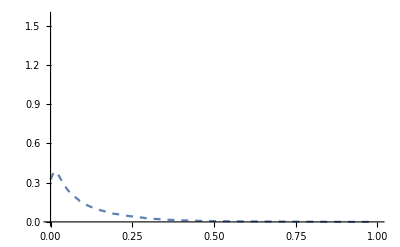

```mathematica
model4=f3[x]*b/a*Exp[-b*x];
fit4=FindFit[bounces[[4]],model4,{a,b},{x}]
f4=Function[{x},model4/.fit4];
Show[
ListLinePlot[bounces[[4]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[f4[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.425977}, {1/100, 0.660285}, {1/50, 0.810531}, {3/100, 0.902011}, {1/25, 0.933438}, {1/20, 0.945136}, {3/50, 0.934449}, {7/100, 0.921476}, {2/25, 0.900596}, {9/100, 0.888919}, {1/10, 0.865887}, {11/100, 0.842813}, {3/25, 0.819797}, « 26 », {39/100, 0.300846}, {2/5, 0.287878}, {41/100, 0.275639}, {21/50, 0.262022}, {43/100, 0.249399}, {11/25, 0.239041}, {9/20, 0.227531}, {23/50, 0.2165}, {47/100, 0.199562}, {12/25, 0.192676}, {49/100, 0.18127}, « 50 »}, « 1 »/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.408861}, {1/100, 0.555072}, {1/50, 0.621534}, {3/100, 0.618379}, {1/25, 0.589468}, {1/20, 0.552344}, {3/50, 0.512544}, {7/100, 0.483144}, {2/25, 0.45174}, {9/100, 0.422908}, {1/10, 0.395255}, {11/100, 0.367594}, {3/25, 0.345897}, « 26 », {39/100, 0.0621454}, {2/5, 0.0577109}, {41/100, 0.0544547}, {21/50, 0.0513253}, {43/100, 0.0477255}, {11/25, 0.0455821}, {9/20, 0.0418072}, {23/50, 0.0389438}, {47/100, 0.0365992}, {12/25, 0.0345651}, {49/100, 0.0318595}, « 50 »}, « 1 »/a, « 1 », {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0.324605}, {1/100, 0.381095}, {1/50, 0.377959}, {3/100, 0.332133}, {1/25, 0.290184}, {1/20, 0.252191}, {3/50, 0.22156}, {7/100, 0.199387}, {2/25, 0.180195}, {9/100, 0.159291}, {1/10, 0.145391}, {11/100, 0.130267}, {3/25, 0.118429}, « 26 », {39/100, 0.0131799}, {2/5, 0.0119823}, {41/100, 0.0112672}, {21/50, 0.0105521}, {43/100, 0.00972625}, {11/25, 0.00931876}, {9/20, 0.00849706}, {23/50, 0.0077615}, {47/100, 0.00750152}, {12/25, 0.0070397}, {49/100, 0.00653841}, « 50 »}, « 2 », {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

FindFit::ivar: 0.2 is not a valid variable.

FindFit[{{0,0.246509},{1/100,0.248737},{1/50,0.212989},{3/100,0.163599},{1/25,0.13153},{1/20,0.106278},{3/50,0.089055},{7/100,0.0766985},{2/25,0.067468},{9/100,0.056317},{1/10,0.0509098},{11/100,0.0444425},{3/25,0.0389985},{13/100,0.0356582},{7/50,0.031676},{3/20,0.0289483},{4/25,0.0264513},{17/100,0.0240067},{9/50,0.0210031},{19/100,0.0190072},{1/5,0.0178692},{21/100,0.0166808},{11/50,0.015348},{23/100,0.0136953},{6/25,0.0126379},{1/4,0.0114719},{13/50,0.00985696},{27/100,0.00961956},{7/25,0.00874379},{29/100,0.00760858},{3/10,0.00674713},{31/100,0.00648962},{8/25,0.00569529},{33/100,0.0054263},{17/50,0.00485125},{7/20,0.00416195},{9/25,0.00398118},{37/100,0.00372243},{19/50,0.00340145},{39/100,0.00326617},{2/5,0.00293595},{41/100,0.00276955},{21/50,0.00261159},{43/100,0.00237331},{11/25,0.00229158},{9/20,0.00209271},{23/50,0.00189443},{47/100,0.00188838},{12/25,0.00176867},{49/100,0.00166341},{1/2,0.00153621},{51/100,0.00145007},{13/25,0.00144246},{53/100,0.00136714},{27/50,0.00124435},{11/20,0.00124391},{14/25,0.00120091},{57/100,0.00119145},{29/50,0.00106196},{59/100,0.000951695},{3/5,0.000936933},{61/100,0.000938509},{31/50,0.000944352},{63/100,0.000803436},{16/25,0.000796699},{13/20,0.000858901},{33/50,0.000781087},{67/100,0.000672615},{17/25,0.000663823},{69/100,0.000715532},{7/10,0.000619849},{71/100,0.000684691},{18/25,0.000643954},{73/100,0.000507308},{37/50,0.000594216},{3/4,0.000539106},{19/25,0.000453257},{77/100,0.000440845},{39/50,0.000383394},{79/100,0.00038313},{4/5,0.000311914},{81/100,0.000295645},{41/50,0.000273032},{83/100,0.000230075},{21/25,0.000201506},{17/20,0.000151643},{43/50,0.000146037},{87/100,0.000120559},{22/25,0.000106346},{89/100,0.0000864839},{9/10,0.0000711735},{91/100,0.0000581109},{23/25,0.0000444084},{93/100,0.000033923},{47/50,0.0000250541},{19/20,0.0000207903},{24/25,0.00001368},{97/100,7.1644×10^-6},{49/50,2.83913×10^-6},{99/100,2.51824×10^-7}},1/a 0.2 ⅇ^(-0.2 x) (1/a 0.2 ⅇ^(-0.2 x) (1/a 0.2 ⅇ^(-0.2 x) ((3.30598 ⅇ^(-0.4 x) (1-x) x)/a/.FindFit[{{0,0.425977},{1/100,0.660285},{1/50,0.810531},{3/100,0.902011},{1/25,0.933438},{1/20,0.945136},{3/50,0.934449},{7/100,0.921476},{2/25,0.900596},{9/100,0.888919},{1/10,0.865887},{11/100,0.842813},{3/25,0.819797},{13/100,0.796926},{7/50,0.773194},{3/20,0.752314},{4/25,0.729294},{17/100,0.709858},{9/50,0.681496},{19/100,0.659109},{1/5,0.642013},{21/100,0.620873},{11/50,0.600027},{23/100,0.581623},{6/25,0.56403},{1/4,0.546134},{13/50,0.524349},{27/100,0.50911},{7/25,0.489011},{29/100,0.466244},{3/10,0.441255},{31/100,0.429854},{8/25,0.408663},{33/100,0.398343},{17/50,0.378073},{7/20,0.352553},{9/25,0.340482},{37/100,0.326232},{19/50,0.310845},{39/100,0.300846},{2/5,0.287878},{41/100,0.275639},{21/50,0.262022},{43/100,0.249399},{11/25,0.239041},{9/20,0.227531},{23/50,0.2165},{47/100,0.199562},{12/25,0.192676},{49/100,0.18127},{1/2,0.171668},{51/100,0.163028},{13/25,0.15243},{53/100,0.147936},{27/50,0.138472},{11/20,0.132807},{14/25,0.126227},{57/100,0.118765},{29/50,0.112923},{59/100,0.104525},{3/5,0.0979519},{61/100,0.0954029},{31/50,0.0894231},{63/100,0.082577},{16/25,0.0783112},{13/20,0.0748249},{33/50,0.0701587},{67/100,0.0653131},{17/25,0.0610211},{69/100,0.059434},{7/10,0.0549731},{71/100,0.0519994},{18/25,0.049824},{73/100,0.0438096},{37/50,0.0430787},{3/4,0.0395766},{19/25,0.0357034},{77/100,0.0341387},{39/50,0.0311613},{79/100,0.0291523},{4/5,0.0260195},{81/100,0.0239228},{41/50,0.0222615},{83/100,0.019242},{21/25,0.0174605},{17/20,0.0147428},{43/50,0.0134814},{87/100,0.0112534},{22/25,0.00982036},{89/100,0.00833437},{9/10,0.00678361},{91/100,0.00544286},{23/25,0.00437493},{93/100,0.00330638},{47/50,0.00240838},{19/20,0.00172409},{24/25,0.00116084},{97/100,0.000666433},{49/50,0.000266133},{99/100,0.0000422741}},(3.30598 ⅇ^(-0.4 x) (1-x) x)/a,{a,0.2},{x}])/.FindFit[{{0,0.408861},{1/100,0.555072},{1/50,0.621534},{3/100,0.618379},{1/25,0.589468},{1/20,0.552344},{3/50,0.512544},{7/100,0.483144},{2/25,0.45174},{9/100,0.422908},{1/10,0.395255},{11/100,0.367594},{3/25,0.345897},{13/100,0.32186},{7/50,0.300651},{3/20,0.284818},{4/25,0.269466},{17/100,0.254672},{9/50,0.234383},{19/100,0.219399},{1/5,0.211001},{21/100,0.199129},{11/50,0.188686},{23/100,0.176538},{6/25,0.167435},{1/4,0.158596},{13/50,0.146056},{27/100,0.139802},{7/25,0.131828},{29/100,0.121186},{3/10,0.111458},{31/100,0.106821},{8/25,0.0981738},{33/100,0.0939639},{17/50,0.0871555},{7/20,0.0773917},{9/25,0.0743363},{37/100,0.069698},{19/50,0.0651416},{39/100,0.0621454},{2/5,0.0577109},{41/100,0.0544547},{21/50,0.0513253},{43/100,0.0477255},{11/25,0.0455821},{9/20,0.0418072},{23/50,0.0389438},{47/100,0.0365992},{12/25,0.0345651},{49/100,0.0318595},{1/2,0.0298814},{51/100,0.0281237},{13/25,0.0263435},{53/100,0.0254139},{27/50,0.0231685},{11/20,0.0224386},{14/25,0.0212264},{57/100,0.0200166},{29/50,0.0188523},{59/100,0.0171664},{3/5,0.016184},{61/100,0.0159498},{31/50,0.0149609},{63/100,0.0136727},{16/25,0.0129881},{13/20,0.0128995},{33/50,0.0117642},{67/100,0.0107224},{17/25,0.0102654},{69/100,0.0103059},{7/10,0.0093958},{71/100,0.00931726},{18/25,0.00875938},{73/100,0.00755142},{37/50,0.00786916},{3/4,0.007178},{19/25,0.00633312},{77/100,0.00613219},{39/50,0.00551879},{79/100,0.00522356},{4/5,0.0045978},{81/100,0.00426884},{41/50,0.0039835},{83/100,0.00342179},{21/25,0.00308476},{17/20,0.00248955},{43/50,0.00234772},{87/100,0.00194671},{22/25,0.00168918},{89/100,0.00141607},{9/10,0.00115016},{91/100,0.000937474},{23/25,0.000738272},{93/100,0.0005532},{47/50,0.000408015},{19/20,0.000307784},{24/25,0.000206436},{97/100,0.000116264},{49/50,0.0000464428},{99/100,6.46993×10^-6}},1/a 0.2 ⅇ^(-0.2 x) ((3.30598 ⅇ^(-0.4 x) (1-x) x)/a/.FindFit[{{0,0.425977},{1/100,0.660285},{1/50,0.810531},{3/100,0.902011},{1/25,0.933438},{1/20,0.945136},{3/50,0.934449},{7/100,0.921476},{2/25,0.900596},{9/100,0.888919},{1/10,0.865887},{11/100,0.842813},{3/25,0.819797},{13/100,0.796926},{7/50,0.773194},{3/20,0.752314},{4/25,0.729294},{17/100,0.709858},{9/50,0.681496},{19/100,0.659109},{1/5,0.642013},{21/100,0.620873},{11/50,0.600027},{23/100,0.581623},{6/25,0.56403},{1/4,0.546134},{13/50,0.524349},{27/100,0.50911},{7/25,0.489011},{29/100,0.466244},{3/10,0.441255},{31/100,0.429854},{8/25,0.408663},{33/100,0.398343},{17/50,0.378073},{7/20,0.352553},{9/25,0.340482},{37/100,0.326232},{19/50,0.310845},{39/100,0.300846},{2/5,0.287878},{41/100,0.275639},{21/50,0.262022},{43/100,0.249399},{11/25,0.239041},{9/20,0.227531},{23/50,0.2165},{47/100,0.199562},{12/25,0.192676},{49/100,0.18127},{1/2,0.171668},{51/100,0.163028},{13/25,0.15243},{53/100,0.147936},{27/50,0.138472},{11/20,0.132807},{14/25,0.126227},{57/100,0.118765},{29/50,0.112923},{59/100,0.104525},{3/5,0.0979519},{61/100,0.0954029},{31/50,0.0894231},{63/100,0.082577},{16/25,0.0783112},{13/20,0.0748249},{33/50,0.0701587},{67/100,0.0653131},{17/25,0.0610211},{69/100,0.059434},{7/10,0.0549731},{71/100,0.0519994},{18/25,0.049824},{73/100,0.0438096},{37/50,0.0430787},{3/4,0.0395766},{19/25,0.0357034},{77/100,0.0341387},{39/50,0.0311613},{79/100,0.0291523},{4/5,0.0260195},{81/100,0.0239228},{41/50,0.0222615},{83/100,0.019242},{21/25,0.0174605},{17/20,0.0147428},{43/50,0.0134814},{87/100,0.0112534},{22/25,0.00982036},{89/100,0.00833437},{9/10,0.00678361},{91/100,0.00544286},{23/25,0.00437493},{93/100,0.00330638},{47/50,0.00240838},{19/20,0.00172409},{24/25,0.00116084},{97/100,0.000666433},{49/50,0.000266133},{99/100,0.0000422741}},(3.30598 ⅇ^(-0.4 x) (1-x) x)/a,{a,0.2},{x}]),{a,0.2},{x}])/.FindFit[{{0,0.324605},{1/100,0.381095},{1/50,0.377959},{3/100,0.332133},{1/25,0.290184},{1/20,0.252191},{3/50,0.22156},{7/100,0.199387},{2/25,0.180195},{9/100,0.159291},{1/10,0.145391},{11/100,0.130267},{3/25,0.118429},{13/100,0.107843},{7/50,0.0980198},{3/20,0.0909749},{4/25,0.0844442},{17/100,0.0779966},{9/50,0.0695699},{19/100,0.0637377},{1/5,0.0606445},{21/100,0.0566665},{11/50,0.0526903},{23/100,0.0480855},{6/25,0.0448775},{1/4,0.0417372},{13/50,0.0368362},{27/100,0.0354826},{7/25,0.0329364},{29/100,0.0291982},{3/10,0.0263575},{31/100,0.0251208},{8/25,0.0224902},{33/100,0.0214355},{17/50,0.0194064},{7/20,0.0168841},{9/25,0.0160783},{37/100,0.0150217},{19/50,0.0138839},{39/100,0.0131799},{2/5,0.0119823},{41/100,0.0112672},{21/50,0.0105521},{43/100,0.00972625},{11/25,0.00931876},{9/20,0.00849706},{23/50,0.0077615},{47/100,0.00750152},{12/25,0.0070397},{49/100,0.00653841},{1/2,0.00607985},{51/100,0.00570941},{13/25,0.00549344},{53/100,0.00525915},{27/50,0.00478761},{11/20,0.00469852},{14/25,0.00449429},{57/100,0.00432204},{29/50,0.00397333},{59/100,0.00358842},{3/5,0.00346153},{61/100,0.00343986},{31/50,0.00333135},{63/100,0.00294805},{16/25,0.00286515},{13/20,0.00296026},{33/50,0.00267979},{67/100,0.00238454},{17/25,0.00231275},{69/100,0.00241701},{7/10,0.00214491},{71/100,0.00225078},{18/25,0.00211002},{73/100,0.00174681},{37/50,0.00192695},{3/4,0.00175916},{19/25,0.00151129},{77/100,0.00146881},{39/50,0.00130418},{79/100,0.00126133},{4/5,0.0010747},{81/100,0.00100883},{41/50,0.000936512},{83/100,0.000801601},{21/25,0.000710161},{17/20,0.000554046},{43/50,0.000530496},{87/100,0.000439313},{22/25,0.000384044},{89/100,0.000316775},{9/10,0.000259412},{91/100,0.000211879},{23/25,0.000164124},{93/100,0.000124667},{47/50,0.0000921414},{19/20,0.0000730373},{24/25,0.0000486754},{97/100,0.0000263472},{49/50,0.0000105653},{99/100,1.20423×10^-6}},1/a 0.2 ⅇ^(-0.2 x) (1/a 0.2 ⅇ^(-0.2 x) ((3.30598 ⅇ^(-0.4 x) (1-x) x)/a/.FindFit[{{0,0.425977},{1/100,0.660285},{1/50,0.810531},{3/100,0.902011},{1/25,0.933438},{1/20,0.945136},{3/50,0.934449},{7/100,0.921476},{2/25,0.900596},{9/100,0.888919},{1/10,0.865887},{11/100,0.842813},{3/25,0.819797},{13/100,0.796926},{7/50,0.773194},{3/20,0.752314},{4/25,0.729294},{17/100,0.709858},{9/50,0.681496},{19/100,0.659109},{1/5,0.642013},{21/100,0.620873},{11/50,0.600027},{23/100,0.581623},{6/25,0.56403},{1/4,0.546134},{13/50,0.524349},{27/100,0.50911},{7/25,0.489011},{29/100,0.466244},{3/10,0.441255},{31/100,0.429854},{8/25,0.408663},{33/100,0.398343},{17/50,0.378073},{7/20,0.352553},{9/25,0.340482},{37/100,0.326232},{19/50,0.310845},{39/100,0.300846},{2/5,0.287878},{41/100,0.275639},{21/50,0.262022},{43/100,0.249399},{11/25,0.239041},{9/20,0.227531},{23/50,0.2165},{47/100,0.199562},{12/25,0.192676},{49/100,0.18127},{1/2,0.171668},{51/100,0.163028},{13/25,0.15243},{53/100,0.147936},{27/50,0.138472},{11/20,0.132807},{14/25,0.126227},{57/100,0.118765},{29/50,0.112923},{59/100,0.104525},{3/5,0.0979519},{61/100,0.0954029},{31/50,0.0894231},{63/100,0.082577},{16/25,0.0783112},{13/20,0.0748249},{33/50,0.0701587},{67/100,0.0653131},{17/25,0.0610211},{69/100,0.059434},{7/10,0.0549731},{71/100,0.0519994},{18/25,0.049824},{73/100,0.0438096},{37/50,0.0430787},{3/4,0.0395766},{19/25,0.0357034},{77/100,0.0341387},{39/50,0.0311613},{79/100,0.0291523},{4/5,0.0260195},{81/100,0.0239228},{41/50,0.0222615},{83/100,0.019242},{21/25,0.0174605},{17/20,0.0147428},{43/50,0.0134814},{87/100,0.0112534},{22/25,0.00982036},{89/100,0.00833437},{9/10,0.00678361},{91/100,0.00544286},{23/25,0.00437493},{93/100,0.00330638},{47/50,0.00240838},{19/20,0.00172409},{24/25,0.00116084},{97/100,0.000666433},{49/50,0.000266133},{99/100,0.0000422741}},(3.30598 ⅇ^(-0.4 x) (1-x) x)/a,{a,0.2},{x}])/.FindFit[{{0,0.408861},{1/100,0.555072},{1/50,0.621534},{3/100,0.618379},{1/25,0.589468},{1/20,0.552344},{3/50,0.512544},{7/100,0.483144},{2/25,0.45174},{9/100,0.422908},{1/10,0.395255},{11/100,0.367594},{3/25,0.345897},{13/100,0.32186},{7/50,0.300651},{3/20,0.284818},{4/25,0.269466},{17/100,0.254672},{9/50,0.234383},{19/100,0.219399},{1/5,0.211001},{21/100,0.199129},{11/50,0.188686},{23/100,0.176538},{6/25,0.167435},{1/4,0.158596},{13/50,0.146056},{27/100,0.139802},{7/25,0.131828},{29/100,0.121186},{3/10,0.111458},{31/100,0.106821},{8/25,0.0981738},{33/100,0.0939639},{17/50,0.0871555},{7/20,0.0773917},{9/25,0.0743363},{37/100,0.069698},{19/50,0.0651416},{39/100,0.0621454},{2/5,0.0577109},{41/100,0.0544547},{21/50,0.0513253},{43/100,0.0477255},{11/25,0.0455821},{9/20,0.0418072},{23/50,0.0389438},{47/100,0.0365992},{12/25,0.0345651},{49/100,0.0318595},{1/2,0.0298814},{51/100,0.0281237},{13/25,0.0263435},{53/100,0.0254139},{27/50,0.0231685},{11/20,0.0224386},{14/25,0.0212264},{57/100,0.0200166},{29/50,0.0188523},{59/100,0.0171664},{3/5,0.016184},{61/100,0.0159498},{31/50,0.0149609},{63/100,0.0136727},{16/25,0.0129881},{13/20,0.0128995},{33/50,0.0117642},{67/100,0.0107224},{17/25,0.0102654},{69/100,0.0103059},{7/10,0.0093958},{71/100,0.00931726},{18/25,0.00875938},{73/100,0.00755142},{37/50,0.00786916},{3/4,0.007178},{19/25,0.00633312},{77/100,0.00613219},{39/50,0.00551879},{79/100,0.00522356},{4/5,0.0045978},{81/100,0.00426884},{41/50,0.0039835},{83/100,0.00342179},{21/25,0.00308476},{17/20,0.00248955},{43/50,0.00234772},{87/100,0.00194671},{22/25,0.00168918},{89/100,0.00141607},{9/10,0.00115016},{91/100,0.000937474},{23/25,0.000738272},{93/100,0.0005532},{47/50,0.000408015},{19/20,0.000307784},{24/25,0.000206436},{97/100,0.000116264},{49/50,0.0000464428},{99/100,6.46993×10^-6}},1/a 0.2 ⅇ^(-0.2 x) ((3.30598 ⅇ^(-0.4 x) (1-x) x)/a/.FindFit[{{0,0.425977},{1/100,0.660285},{1/50,0.810531},{3/100,0.902011},{1/25,0.933438},{1/20,0.945136},{3/50,0.934449},{7/100,0.921476},{2/25,0.900596},{9/100,0.888919},{1/10,0.865887},{11/100,0.842813},{3/25,0.819797},{13/100,0.796926},{7/50,0.773194},{3/20,0.752314},{4/25,0.729294},{17/100,0.709858},{9/50,0.681496},{19/100,0.659109},{1/5,0.642013},{21/100,0.620873},{11/50,0.600027},{23/100,0.581623},{6/25,0.56403},{1/4,0.546134},{13/50,0.524349},{27/100,0.50911},{7/25,0.489011},{29/100,0.466244},{3/10,0.441255},{31/100,0.429854},{8/25,0.408663},{33/100,0.398343},{17/50,0.378073},{7/20,0.352553},{9/25,0.340482},{37/100,0.326232},{19/50,0.310845},{39/100,0.300846},{2/5,0.287878},{41/100,0.275639},{21/50,0.262022},{43/100,0.249399},{11/25,0.239041},{9/20,0.227531},{23/50,0.2165},{47/100,0.199562},{12/25,0.192676},{49/100,0.18127},{1/2,0.171668},{51/100,0.163028},{13/25,0.15243},{53/100,0.147936},{27/50,0.138472},{11/20,0.132807},{14/25,0.126227},{57/100,0.118765},{29/50,0.112923},{59/100,0.104525},{3/5,0.0979519},{61/100,0.0954029},{31/50,0.0894231},{63/100,0.082577},{16/25,0.0783112},{13/20,0.0748249},{33/50,0.0701587},{67/100,0.0653131},{17/25,0.0610211},{69/100,0.059434},{7/10,0.0549731},{71/100,0.0519994},{18/25,0.049824},{73/100,0.0438096},{37/50,0.0430787},{3/4,0.0395766},{19/25,0.0357034},{77/100,0.0341387},{39/50,0.0311613},{79/100,0.0291523},{4/5,0.0260195},{81/100,0.0239228},{41/50,0.0222615},{83/100,0.019242},{21/25,0.0174605},{17/20,0.0147428},{43/50,0.0134814},{87/100,0.0112534},{22/25,0.00982036},{89/100,0.00833437},{9/10,0.00678361},{91/100,0.00544286},{23/25,0.00437493},{93/100,0.00330638},{47/50,0.00240838},{19/20,0.00172409},{24/25,0.00116084},{97/100,0.000666433},{49/50,0.000266133},{99/100,0.0000422741}},(3.30598 ⅇ^(-0.4 x) (1-x) x)/a,{a,0.2},{x}]),{a,0.2},{x}]),{a,0.2},{x}]),{a,0.2},{x}]

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.425977}, {1/100, 0.660285}, {1/50, 0.810531}, {3/100, 0.902011}, {1/25, 0.933438}, {1/20, 0.945136}, {3/50, 0.934449}, {7/100, 0.921476}, {2/25, 0.900596}, {9/100, 0.888919}, {1/10, 0.865887}, {11/100, 0.842813}, {3/25, 0.819797}, « 26 », {39/100, 0.300846}, {2/5, 0.287878}, {41/100, 0.275639}, {21/50, 0.262022}, {43/100, 0.249399}, {11/25, 0.239041}, {9/20, 0.227531}, {23/50, 0.2165}, {47/100, 0.199562}, {12/25, 0.192676}, {49/100, 0.18127}, « 50 »}, « 22 »/a, {a, 0.2}, {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.425977}, {1/100, 0.660285}, {1/50, 0.810531}, {3/100, 0.902011}, {1/25, 0.933438}, {1/20, 0.945136}, {3/50, 0.934449}, {7/100, 0.921476}, {2/25, 0.900596}, {9/100, 0.888919}, {1/10, 0.865887}, {11/100, 0.842813}, {3/25, 0.819797}, « 26 », {39/100, 0.300846}, {2/5, 0.287878}, {41/100, 0.275639}, {21/50, 0.262022}, {43/100, 0.249399}, {11/25, 0.239041}, {9/20, 0.227531}, {23/50, 0.2165}, {47/100, 0.199562}, {12/25, 0.192676}, {49/100, 0.18127}, « 50 »}, « 22 »/a, {a, 0.2}, {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0.408861}, {1/100, 0.555072}, {1/50, 0.621534}, {3/100, 0.618379}, {1/25, 0.589468}, {1/20, 0.552344}, {3/50, 0.512544}, {7/100, 0.483144}, {2/25, 0.45174}, {9/100, 0.422908}, {1/10, 0.395255}, {11/100, 0.367594}, {3/25, 0.345897}, « 26 », {39/100, 0.0621454}, {2/5, 0.0577109}, {41/100, 0.0544547}, {21/50, 0.0513253}, {43/100, 0.0477255}, {11/25, 0.0455821}, {9/20, 0.0418072}, {23/50, 0.0389438}, {47/100, 0.0365992}, {12/25, 0.0345651}, {49/100, 0.0318595}, « 50 »}, « 1 »/a, « 1 », {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

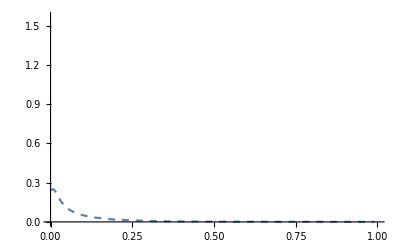

```mathematica
model5=f4[x]*b/a*Exp[-b*x];
fit5=FindFit[bounces[[5]],model5,{a,b},{x}]
f5=Function[{x},model5/.fit5];
Show[
ListLinePlot[bounces[[5]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[f5[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

FindFit::ivar: 0.2 is not a valid variable.

FindFit[{{0,0.246685},{1/100,0.454639},{1/50,0.621233},{3/100,0.774937},{1/25,0.865385},{1/20,0.945319},{3/50,1.01961},{7/100,1.06215},{2/25,1.10749},{9/100,1.14568},{1/10,1.17656},{11/100,1.20788},{3/25,1.22484},{13/100,1.24346},{7/50,1.2682},{3/20,1.27292},{4/25,1.28356},{17/100,1.29015},{9/50,1.31336},{19/100,1.31742},{1/5,1.31302},{21/100,1.31462},{11/50,1.31915},{23/100,1.32321},{6/25,1.31296},{1/4,1.30656},{13/50,1.31171},{27/100,1.29894},{7/25,1.2972},{29/100,1.27978},{3/10,1.27876},{31/100,1.25923},{8/25,1.25941},{33/100,1.24001},{17/50,1.22598},{7/20,1.2288},{9/25,1.20202},{37/100,1.17926},{19/50,1.15617},{39/100,1.14221},{2/5,1.12608},{41/100,1.10332},{21/50,1.06482},{43/100,1.05874},{11/25,1.02301},{9/20,1.02041},{23/50,1.00946},{47/100,0.956672},{12/25,0.945638},{49/100,0.930258},{1/2,0.890772},{51/100,0.867026},{13/25,0.844581},{53/100,0.820488},{27/50,0.805247},{11/20,0.774558},{14/25,0.749201},{57/100,0.730348},{29/50,0.704338},{59/100,0.68318},{3/5,0.652516},{61/100,0.643004},{31/50,0.613978},{63/100,0.591334},{16/25,0.56465},{13/20,0.532988},{33/50,0.518701},{67/100,0.497644},{17/25,0.471238},{69/100,0.449681},{7/10,0.428682},{71/100,0.403644},{18/25,0.378137},{73/100,0.360631},{37/50,0.338719},{3/4,0.319989},{19/25,0.300171},{77/100,0.281555},{39/50,0.260014},{79/100,0.241643},{4/5,0.224615},{81/100,0.202889},{41/50,0.187077},{83/100,0.171484},{21/25,0.152818},{17/20,0.137808},{43/50,0.121752},{87/100,0.107591},{22/25,0.0930013},{89/100,0.0804007},{9/10,0.0682845},{91/100,0.0559822},{23/25,0.0443282},{93/100,0.0370672},{47/50,0.0288954},{19/20,0.020041},{24/25,0.013499},{97/100,0.00803869},{49/50,0.00392339},{99/100,0.000823254}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}]

ReplaceAll::reps: {FindFit[{{0, 0.246685}, {1/100, 0.454639}, {1/50, 0.621233}, {3/100, 0.774937}, {1/25, 0.865385}, {1/20, 0.945319}, {3/50, 1.01961}, {7/100, 1.06215}, {2/25, 1.10749}, {9/100, 1.14568}, {1/10, 1.17656}, {11/100, 1.20788}, {3/25, 1.22484}, « 25 », {19/50, 1.15617}, {39/100, 1.14221}, {2/5, 1.12608}, {41/100, 1.10332}, {21/50, 1.06482}, {43/100, 1.05874}, {11/25, 1.02301}, {9/20, 1.02041}, {23/50, 1.00946}, {47/100, 0.956672}, {12/25, 0.945638}, {49/100, 0.930258}, « 50 »}, « 2 », {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

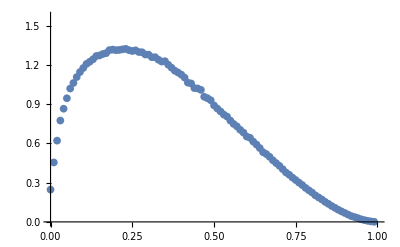

```mathematica
modelFit1=FindFit[bounces[[1]], model,{a,b},{x}]
bounce1=Function[{x},Evaluate[model/.modelFit1]];
Show[
ListPlot[bounces[[1]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce1[x],{x,0,1},PlotStyle->Red]
]
```

FindFit::ivar: 0.2 is not a valid variable.

FindFit[{{0,0.425977},{1/100,0.660285},{1/50,0.810531},{3/100,0.902011},{1/25,0.933438},{1/20,0.945136},{3/50,0.934449},{7/100,0.921476},{2/25,0.900596},{9/100,0.888919},{1/10,0.865887},{11/100,0.842813},{3/25,0.819797},{13/100,0.796926},{7/50,0.773194},{3/20,0.752314},{4/25,0.729294},{17/100,0.709858},{9/50,0.681496},{19/100,0.659109},{1/5,0.642013},{21/100,0.620873},{11/50,0.600027},{23/100,0.581623},{6/25,0.56403},{1/4,0.546134},{13/50,0.524349},{27/100,0.50911},{7/25,0.489011},{29/100,0.466244},{3/10,0.441255},{31/100,0.429854},{8/25,0.408663},{33/100,0.398343},{17/50,0.378073},{7/20,0.352553},{9/25,0.340482},{37/100,0.326232},{19/50,0.310845},{39/100,0.300846},{2/5,0.287878},{41/100,0.275639},{21/50,0.262022},{43/100,0.249399},{11/25,0.239041},{9/20,0.227531},{23/50,0.2165},{47/100,0.199562},{12/25,0.192676},{49/100,0.18127},{1/2,0.171668},{51/100,0.163028},{13/25,0.15243},{53/100,0.147936},{27/50,0.138472},{11/20,0.132807},{14/25,0.126227},{57/100,0.118765},{29/50,0.112923},{59/100,0.104525},{3/5,0.0979519},{61/100,0.0954029},{31/50,0.0894231},{63/100,0.082577},{16/25,0.0783112},{13/20,0.0748249},{33/50,0.0701587},{67/100,0.0653131},{17/25,0.0610211},{69/100,0.059434},{7/10,0.0549731},{71/100,0.0519994},{18/25,0.049824},{73/100,0.0438096},{37/50,0.0430787},{3/4,0.0395766},{19/25,0.0357034},{77/100,0.0341387},{39/50,0.0311613},{79/100,0.0291523},{4/5,0.0260195},{81/100,0.0239228},{41/50,0.0222615},{83/100,0.019242},{21/25,0.0174605},{17/20,0.0147428},{43/50,0.0134814},{87/100,0.0112534},{22/25,0.00982036},{89/100,0.00833437},{9/10,0.00678361},{91/100,0.00544286},{23/25,0.00437493},{93/100,0.00330638},{47/50,0.00240838},{19/20,0.00172409},{24/25,0.00116084},{97/100,0.000666433},{49/50,0.000266133},{99/100,0.0000422741}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}]

ReplaceAll::reps: {FindFit[{{0, 0.425977}, {1/100, 0.660285}, {1/50, 0.810531}, {3/100, 0.902011}, {1/25, 0.933438}, {1/20, 0.945136}, {3/50, 0.934449}, {7/100, 0.921476}, {2/25, 0.900596}, {9/100, 0.888919}, {1/10, 0.865887}, {11/100, 0.842813}, {3/25, 0.819797}, « 26 », {39/100, 0.300846}, {2/5, 0.287878}, {41/100, 0.275639}, {21/50, 0.262022}, {43/100, 0.249399}, {11/25, 0.239041}, {9/20, 0.227531}, {23/50, 0.2165}, {47/100, 0.199562}, {12/25, 0.192676}, {49/100, 0.18127}, « 50 »}, « 1 »/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.425977}, {1/100, 0.660285}, {1/50, 0.810531}, {3/100, 0.902011}, {1/25, 0.933438}, {1/20, 0.945136}, {3/50, 0.934449}, {7/100, 0.921476}, {2/25, 0.900596}, {9/100, 0.888919}, {1/10, 0.865887}, {11/100, 0.842813}, {3/25, 0.819797}, « 26 », {39/100, 0.300846}, {2/5, 0.287878}, {41/100, 0.275639}, {21/50, 0.262022}, {43/100, 0.249399}, {11/25, 0.239041}, {9/20, 0.227531}, {23/50, 0.2165}, {47/100, 0.199562}, {12/25, 0.192676}, {49/100, 0.18127}, « 50 »}, « 22 »/a, {a, 0.2}, {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0.425977}, {1/100, 0.660285}, {1/50, 0.810531}, {3/100, 0.902011}, {1/25, 0.933438}, {1/20, 0.945136}, {3/50, 0.934449}, {7/100, 0.921476}, {2/25, 0.900596}, {9/100, 0.888919}, {1/10, 0.865887}, {11/100, 0.842813}, {3/25, 0.819797}, « 26 », {39/100, 0.300846}, {2/5, 0.287878}, {41/100, 0.275639}, {21/50, 0.262022}, {43/100, 0.249399}, {11/25, 0.239041}, {9/20, 0.227531}, {23/50, 0.2165}, {47/100, 0.199562}, {12/25, 0.192676}, {49/100, 0.18127}, « 50 »}, « 2 », {0.0204286}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

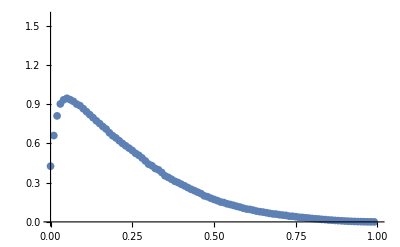

```mathematica
modelFit2=FindFit[bounces[[2]], model,{a,b},{x}]
bounce2=Function[{x},Evaluate[model/.modelFit2]];
Show[
ListPlot[bounces[[2]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce2[x],{x,0,1},PlotStyle->Red]
]
```

FindFit::ivar: 0.2 is not a valid variable.

FindFit[{{0,0.408861},{1/100,0.555072},{1/50,0.621534},{3/100,0.618379},{1/25,0.589468},{1/20,0.552344},{3/50,0.512544},{7/100,0.483144},{2/25,0.45174},{9/100,0.422908},{1/10,0.395255},{11/100,0.367594},{3/25,0.345897},{13/100,0.32186},{7/50,0.300651},{3/20,0.284818},{4/25,0.269466},{17/100,0.254672},{9/50,0.234383},{19/100,0.219399},{1/5,0.211001},{21/100,0.199129},{11/50,0.188686},{23/100,0.176538},{6/25,0.167435},{1/4,0.158596},{13/50,0.146056},{27/100,0.139802},{7/25,0.131828},{29/100,0.121186},{3/10,0.111458},{31/100,0.106821},{8/25,0.0981738},{33/100,0.0939639},{17/50,0.0871555},{7/20,0.0773917},{9/25,0.0743363},{37/100,0.069698},{19/50,0.0651416},{39/100,0.0621454},{2/5,0.0577109},{41/100,0.0544547},{21/50,0.0513253},{43/100,0.0477255},{11/25,0.0455821},{9/20,0.0418072},{23/50,0.0389438},{47/100,0.0365992},{12/25,0.0345651},{49/100,0.0318595},{1/2,0.0298814},{51/100,0.0281237},{13/25,0.0263435},{53/100,0.0254139},{27/50,0.0231685},{11/20,0.0224386},{14/25,0.0212264},{57/100,0.0200166},{29/50,0.0188523},{59/100,0.0171664},{3/5,0.016184},{61/100,0.0159498},{31/50,0.0149609},{63/100,0.0136727},{16/25,0.0129881},{13/20,0.0128995},{33/50,0.0117642},{67/100,0.0107224},{17/25,0.0102654},{69/100,0.0103059},{7/10,0.0093958},{71/100,0.00931726},{18/25,0.00875938},{73/100,0.00755142},{37/50,0.00786916},{3/4,0.007178},{19/25,0.00633312},{77/100,0.00613219},{39/50,0.00551879},{79/100,0.00522356},{4/5,0.0045978},{81/100,0.00426884},{41/50,0.0039835},{83/100,0.00342179},{21/25,0.00308476},{17/20,0.00248955},{43/50,0.00234772},{87/100,0.00194671},{22/25,0.00168918},{89/100,0.00141607},{9/10,0.00115016},{91/100,0.000937474},{23/25,0.000738272},{93/100,0.0005532},{47/50,0.000408015},{19/20,0.000307784},{24/25,0.000206436},{97/100,0.000116264},{49/50,0.0000464428},{99/100,6.46993×10^-6}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}]

ReplaceAll::reps: {FindFit[{{0, 0.408861}, {1/100, 0.555072}, {1/50, 0.621534}, {3/100, 0.618379}, {1/25, 0.589468}, {1/20, 0.552344}, {3/50, 0.512544}, {7/100, 0.483144}, {2/25, 0.45174}, {9/100, 0.422908}, {1/10, 0.395255}, {11/100, 0.367594}, {3/25, 0.345897}, « 26 », {39/100, 0.0621454}, {2/5, 0.0577109}, {41/100, 0.0544547}, {21/50, 0.0513253}, {43/100, 0.0477255}, {11/25, 0.0455821}, {9/20, 0.0418072}, {23/50, 0.0389438}, {47/100, 0.0365992}, {12/25, 0.0345651}, {49/100, 0.0318595}, « 50 »}, « 1 »/a, « 1 », {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.408861}, {1/100, 0.555072}, {1/50, 0.621534}, {3/100, 0.618379}, {1/25, 0.589468}, {1/20, 0.552344}, {3/50, 0.512544}, {7/100, 0.483144}, {2/25, 0.45174}, {9/100, 0.422908}, {1/10, 0.395255}, {11/100, 0.367594}, {3/25, 0.345897}, « 26 », {39/100, 0.0621454}, {2/5, 0.0577109}, {41/100, 0.0544547}, {21/50, 0.0513253}, {43/100, 0.0477255}, {11/25, 0.0455821}, {9/20, 0.0418072}, {23/50, 0.0389438}, {47/100, 0.0365992}, {12/25, 0.0345651}, {49/100, 0.0318595}, « 50 »}, « 22 »/a, « 1 », {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0., 0.408861}, {0.01, 0.555072}, {0.02, 0.621534}, {0.03, 0.618379}, {0.04, 0.589468}, {0.05, 0.552344}, {0.06, 0.512544}, {0.07, 0.483144}, {0.08, 0.45174}, {0.09, 0.422908}, {0.1, 0.395255}, {0.11, 0.367594}, « 27 », {0.39, 0.0621454}, {0.4, 0.0577109}, {0.41, 0.0544547}, {0.42, 0.0513253}, {0.43, 0.0477255}, {0.44, 0.0455821}, {0.45, 0.0418072}, {0.46, 0.0389438}, {0.47, 0.0365992}, {0.48, 0.0345651}, {0.49, 0.0318595}, « 50 »}, « 22 »/a, « 1 », {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0.408861}, {1/100, 0.555072}, {1/50, 0.621534}, {3/100, 0.618379}, {1/25, 0.589468}, {1/20, 0.552344}, {3/50, 0.512544}, {7/100, 0.483144}, {2/25, 0.45174}, {9/100, 0.422908}, {1/10, 0.395255}, {11/100, 0.367594}, {3/25, 0.345897}, « 26 », {39/100, 0.0621454}, {2/5, 0.0577109}, {41/100, 0.0544547}, {21/50, 0.0513253}, {43/100, 0.0477255}, {11/25, 0.0455821}, {9/20, 0.0418072}, {23/50, 0.0389438}, {47/100, 0.0365992}, {12/25, 0.0345651}, {49/100, 0.0318595}, « 50 »}, « 22 »/a, « 1 », {« 20 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

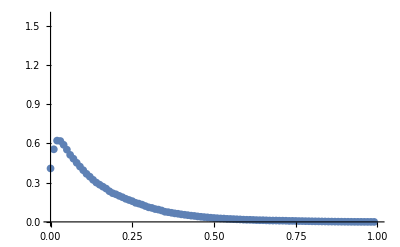

```mathematica
modelFit3=FindFit[bounces[[3]], model,{a,b},{x}]
bounce3=Function[{x},Evaluate[model/.modelFit3]];
Show[
ListPlot[bounces[[3]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce3[x],{x,0,1},PlotStyle->Red]
]
```

FindFit::ivar: 0.2 is not a valid variable.

FindFit[{{0,0.324605},{1/100,0.381095},{1/50,0.377959},{3/100,0.332133},{1/25,0.290184},{1/20,0.252191},{3/50,0.22156},{7/100,0.199387},{2/25,0.180195},{9/100,0.159291},{1/10,0.145391},{11/100,0.130267},{3/25,0.118429},{13/100,0.107843},{7/50,0.0980198},{3/20,0.0909749},{4/25,0.0844442},{17/100,0.0779966},{9/50,0.0695699},{19/100,0.0637377},{1/5,0.0606445},{21/100,0.0566665},{11/50,0.0526903},{23/100,0.0480855},{6/25,0.0448775},{1/4,0.0417372},{13/50,0.0368362},{27/100,0.0354826},{7/25,0.0329364},{29/100,0.0291982},{3/10,0.0263575},{31/100,0.0251208},{8/25,0.0224902},{33/100,0.0214355},{17/50,0.0194064},{7/20,0.0168841},{9/25,0.0160783},{37/100,0.0150217},{19/50,0.0138839},{39/100,0.0131799},{2/5,0.0119823},{41/100,0.0112672},{21/50,0.0105521},{43/100,0.00972625},{11/25,0.00931876},{9/20,0.00849706},{23/50,0.0077615},{47/100,0.00750152},{12/25,0.0070397},{49/100,0.00653841},{1/2,0.00607985},{51/100,0.00570941},{13/25,0.00549344},{53/100,0.00525915},{27/50,0.00478761},{11/20,0.00469852},{14/25,0.00449429},{57/100,0.00432204},{29/50,0.00397333},{59/100,0.00358842},{3/5,0.00346153},{61/100,0.00343986},{31/50,0.00333135},{63/100,0.00294805},{16/25,0.00286515},{13/20,0.00296026},{33/50,0.00267979},{67/100,0.00238454},{17/25,0.00231275},{69/100,0.00241701},{7/10,0.00214491},{71/100,0.00225078},{18/25,0.00211002},{73/100,0.00174681},{37/50,0.00192695},{3/4,0.00175916},{19/25,0.00151129},{77/100,0.00146881},{39/50,0.00130418},{79/100,0.00126133},{4/5,0.0010747},{81/100,0.00100883},{41/50,0.000936512},{83/100,0.000801601},{21/25,0.000710161},{17/20,0.000554046},{43/50,0.000530496},{87/100,0.000439313},{22/25,0.000384044},{89/100,0.000316775},{9/10,0.000259412},{91/100,0.000211879},{23/25,0.000164124},{93/100,0.000124667},{47/50,0.0000921414},{19/20,0.0000730373},{24/25,0.0000486754},{97/100,0.0000263472},{49/50,0.0000105653},{99/100,1.20423×10^-6}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}]

ReplaceAll::reps: {FindFit[{{0, 0.324605}, {1/100, 0.381095}, {1/50, 0.377959}, {3/100, 0.332133}, {1/25, 0.290184}, {1/20, 0.252191}, {3/50, 0.22156}, {7/100, 0.199387}, {2/25, 0.180195}, {9/100, 0.159291}, {1/10, 0.145391}, {11/100, 0.130267}, {3/25, 0.118429}, « 26 », {39/100, 0.0131799}, {2/5, 0.0119823}, {41/100, 0.0112672}, {21/50, 0.0105521}, {43/100, 0.00972625}, {11/25, 0.00931876}, {9/20, 0.00849706}, {23/50, 0.0077615}, {47/100, 0.00750152}, {12/25, 0.0070397}, {49/100, 0.00653841}, « 50 »}, « 2 », {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0., 0.324605}, {0.01, 0.381095}, {0.02, 0.377959}, {0.03, 0.332133}, {0.04, 0.290184}, {0.05, 0.252191}, {0.06, 0.22156}, {0.07, 0.199387}, {0.08, 0.180195}, {0.09, 0.159291}, {0.1, 0.145391}, {0.11, 0.130267}, « 27 », {0.39, 0.0131799}, {0.4, 0.0119823}, {0.41, 0.0112672}, {0.42, 0.0105521}, {0.43, 0.00972625}, {0.44, 0.00931876}, {0.45, 0.00849706}, {0.46, 0.0077615}, {0.47, 0.00750152}, {0.48, 0.0070397}, {0.49, 0.00653841}, « 50 »}, « 2 », {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

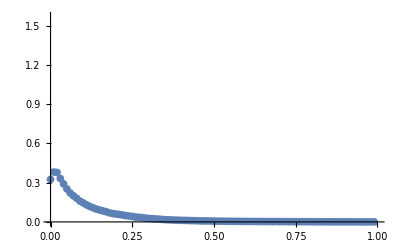

```mathematica
modelFit4=FindFit[bounces[[4]], model,{a,b},{x}]
bounce4=Function[{x},Evaluate[model/.modelFit4]];
Show[
ListPlot[bounces[[4]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce4[x],{x,0,1},PlotStyle->Red]
]
```

```mathematica
coeffsA={a/.modelFit1,a/.modelFit2,a/.modelFit3,a/.modelFit4}
coeffsB={b/.modelFit1,b/.modelFit2,b/.modelFit3,b/.modelFit4}
ListPlot[coeffsA]
ListPlot[coeffsB]
```

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.246685}, {1/100, 0.454639}, {1/50, 0.621233}, {3/100, 0.774937}, {1/25, 0.865385}, {1/20, 0.945319}, {3/50, 1.01961}, {7/100, 1.06215}, {2/25, 1.10749}, {9/100, 1.14568}, {1/10, 1.17656}, {11/100, 1.20788}, {3/25, 1.22484}, « 25 », {19/50, 1.15617}, {39/100, 1.14221}, {2/5, 1.12608}, {41/100, 1.10332}, {21/50, 1.06482}, {43/100, 1.05874}, {11/25, 1.02301}, {9/20, 1.02041}, {23/50, 1.00946}, {47/100, 0.956672}, {12/25, 0.945638}, {49/100, 0.930258}, « 50 »}, « 2 », {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.425977}, {1/100, 0.660285}, {1/50, 0.810531}, {3/100, 0.902011}, {1/25, 0.933438}, {1/20, 0.945136}, {3/50, 0.934449}, {7/100, 0.921476}, {2/25, 0.900596}, {9/100, 0.888919}, {1/10, 0.865887}, {11/100, 0.842813}, {3/25, 0.819797}, « 26 », {39/100, 0.300846}, {2/5, 0.287878}, {41/100, 0.275639}, {21/50, 0.262022}, {43/100, 0.249399}, {11/25, 0.239041}, {9/20, 0.227531}, {23/50, 0.2165}, {47/100, 0.199562}, {12/25, 0.192676}, {49/100, 0.18127}, « 50 »}, « 1 »/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0.408861}, {1/100, 0.555072}, {1/50, 0.621534}, {3/100, 0.618379}, {1/25, 0.589468}, {1/20, 0.552344}, {3/50, 0.512544}, {7/100, 0.483144}, {2/25, 0.45174}, {9/100, 0.422908}, {1/10, 0.395255}, {11/100, 0.367594}, {3/25, 0.345897}, « 26 », {39/100, 0.0621454}, {2/5, 0.0577109}, {41/100, 0.0544547}, {21/50, 0.0513253}, {43/100, 0.0477255}, {11/25, 0.0455821}, {9/20, 0.0418072}, {23/50, 0.0389438}, {47/100, 0.0365992}, {12/25, 0.0345651}, {49/100, 0.0318595}, « 50 »}, « 1 »/a, « 1 », {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

{a/.FindFit[{{0,0.246685},{1/100,0.454639},{1/50,0.621233},{3/100,0.774937},{1/25,0.865385},{1/20,0.945319},{3/50,1.01961},{7/100,1.06215},{2/25,1.10749},{9/100,1.14568},{1/10,1.17656},{11/100,1.20788},{3/25,1.22484},{13/100,1.24346},{7/50,1.2682},{3/20,1.27292},{4/25,1.28356},{17/100,1.29015},{9/50,1.31336},{19/100,1.31742},{1/5,1.31302},{21/100,1.31462},{11/50,1.31915},{23/100,1.32321},{6/25,1.31296},{1/4,1.30656},{13/50,1.31171},{27/100,1.29894},{7/25,1.2972},{29/100,1.27978},{3/10,1.27876},{31/100,1.25923},{8/25,1.25941},{33/100,1.24001},{17/50,1.22598},{7/20,1.2288},{9/25,1.20202},{37/100,1.17926},{19/50,1.15617},{39/100,1.14221},{2/5,1.12608},{41/100,1.10332},{21/50,1.06482},{43/100,1.05874},{11/25,1.02301},{9/20,1.02041},{23/50,1.00946},{47/100,0.956672},{12/25,0.945638},{49/100,0.930258},{1/2,0.890772},{51/100,0.867026},{13/25,0.844581},{53/100,0.820488},{27/50,0.805247},{11/20,0.774558},{14/25,0.749201},{57/100,0.730348},{29/50,0.704338},{59/100,0.68318},{3/5,0.652516},{61/100,0.643004},{31/50,0.613978},{63/100,0.591334},{16/25,0.56465},{13/20,0.532988},{33/50,0.518701},{67/100,0.497644},{17/25,0.471238},{69/100,0.449681},{7/10,0.428682},{71/100,0.403644},{18/25,0.378137},{73/100,0.360631},{37/50,0.338719},{3/4,0.319989},{19/25,0.300171},{77/100,0.281555},{39/50,0.260014},{79/100,0.241643},{4/5,0.224615},{81/100,0.202889},{41/50,0.187077},{83/100,0.171484},{21/25,0.152818},{17/20,0.137808},{43/50,0.121752},{87/100,0.107591},{22/25,0.0930013},{89/100,0.0804007},{9/10,0.0682845},{91/100,0.0559822},{23/25,0.0443282},{93/100,0.0370672},{47/50,0.0288954},{19/20,0.020041},{24/25,0.013499},{97/100,0.00803869},{49/50,0.00392339},{99/100,0.000823254}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}],a/.FindFit[{{0,0.425977},{1/100,0.660285},{1/50,0.810531},{3/100,0.902011},{1/25,0.933438},{1/20,0.945136},{3/50,0.934449},{7/100,0.921476},{2/25,0.900596},{9/100,0.888919},{1/10,0.865887},{11/100,0.842813},{3/25,0.819797},{13/100,0.796926},{7/50,0.773194},{3/20,0.752314},{4/25,0.729294},{17/100,0.709858},{9/50,0.681496},{19/100,0.659109},{1/5,0.642013},{21/100,0.620873},{11/50,0.600027},{23/100,0.581623},{6/25,0.56403},{1/4,0.546134},{13/50,0.524349},{27/100,0.50911},{7/25,0.489011},{29/100,0.466244},{3/10,0.441255},{31/100,0.429854},{8/25,0.408663},{33/100,0.398343},{17/50,0.378073},{7/20,0.352553},{9/25,0.340482},{37/100,0.326232},{19/50,0.310845},{39/100,0.300846},{2/5,0.287878},{41/100,0.275639},{21/50,0.262022},{43/100,0.249399},{11/25,0.239041},{9/20,0.227531},{23/50,0.2165},{47/100,0.199562},{12/25,0.192676},{49/100,0.18127},{1/2,0.171668},{51/100,0.163028},{13/25,0.15243},{53/100,0.147936},{27/50,0.138472},{11/20,0.132807},{14/25,0.126227},{57/100,0.118765},{29/50,0.112923},{59/100,0.104525},{3/5,0.0979519},{61/100,0.0954029},{31/50,0.0894231},{63/100,0.082577},{16/25,0.0783112},{13/20,0.0748249},{33/50,0.0701587},{67/100,0.0653131},{17/25,0.0610211},{69/100,0.059434},{7/10,0.0549731},{71/100,0.0519994},{18/25,0.049824},{73/100,0.0438096},{37/50,0.0430787},{3/4,0.0395766},{19/25,0.0357034},{77/100,0.0341387},{39/50,0.0311613},{79/100,0.0291523},{4/5,0.0260195},{81/100,0.0239228},{41/50,0.0222615},{83/100,0.019242},{21/25,0.0174605},{17/20,0.0147428},{43/50,0.0134814},{87/100,0.0112534},{22/25,0.00982036},{89/100,0.00833437},{9/10,0.00678361},{91/100,0.00544286},{23/25,0.00437493},{93/100,0.00330638},{47/50,0.00240838},{19/20,0.00172409},{24/25,0.00116084},{97/100,0.000666433},{49/50,0.000266133},{99/100,0.0000422741}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}],a/.FindFit[{{0,0.408861},{1/100,0.555072},{1/50,0.621534},{3/100,0.618379},{1/25,0.589468},{1/20,0.552344},{3/50,0.512544},{7/100,0.483144},{2/25,0.45174},{9/100,0.422908},{1/10,0.395255},{11/100,0.367594},{3/25,0.345897},{13/100,0.32186},{7/50,0.300651},{3/20,0.284818},{4/25,0.269466},{17/100,0.254672},{9/50,0.234383},{19/100,0.219399},{1/5,0.211001},{21/100,0.199129},{11/50,0.188686},{23/100,0.176538},{6/25,0.167435},{1/4,0.158596},{13/50,0.146056},{27/100,0.139802},{7/25,0.131828},{29/100,0.121186},{3/10,0.111458},{31/100,0.106821},{8/25,0.0981738},{33/100,0.0939639},{17/50,0.0871555},{7/20,0.0773917},{9/25,0.0743363},{37/100,0.069698},{19/50,0.0651416},{39/100,0.0621454},{2/5,0.0577109},{41/100,0.0544547},{21/50,0.0513253},{43/100,0.0477255},{11/25,0.0455821},{9/20,0.0418072},{23/50,0.0389438},{47/100,0.0365992},{12/25,0.0345651},{49/100,0.0318595},{1/2,0.0298814},{51/100,0.0281237},{13/25,0.0263435},{53/100,0.0254139},{27/50,0.0231685},{11/20,0.0224386},{14/25,0.0212264},{57/100,0.0200166},{29/50,0.0188523},{59/100,0.0171664},{3/5,0.016184},{61/100,0.0159498},{31/50,0.0149609},{63/100,0.0136727},{16/25,0.0129881},{13/20,0.0128995},{33/50,0.0117642},{67/100,0.0107224},{17/25,0.0102654},{69/100,0.0103059},{7/10,0.0093958},{71/100,0.00931726},{18/25,0.00875938},{73/100,0.00755142},{37/50,0.00786916},{3/4,0.007178},{19/25,0.00633312},{77/100,0.00613219},{39/50,0.00551879},{79/100,0.00522356},{4/5,0.0045978},{81/100,0.00426884},{41/50,0.0039835},{83/100,0.00342179},{21/25,0.00308476},{17/20,0.00248955},{43/50,0.00234772},{87/100,0.00194671},{22/25,0.00168918},{89/100,0.00141607},{9/10,0.00115016},{91/100,0.000937474},{23/25,0.000738272},{93/100,0.0005532},{47/50,0.000408015},{19/20,0.000307784},{24/25,0.000206436},{97/100,0.000116264},{49/50,0.0000464428},{99/100,6.46993×10^-6}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}],a/.FindFit[{{0,0.324605},{1/100,0.381095},{1/50,0.377959},{3/100,0.332133},{1/25,0.290184},{1/20,0.252191},{3/50,0.22156},{7/100,0.199387},{2/25,0.180195},{9/100,0.159291},{1/10,0.145391},{11/100,0.130267},{3/25,0.118429},{13/100,0.107843},{7/50,0.0980198},{3/20,0.0909749},{4/25,0.0844442},{17/100,0.0779966},{9/50,0.0695699},{19/100,0.0637377},{1/5,0.0606445},{21/100,0.0566665},{11/50,0.0526903},{23/100,0.0480855},{6/25,0.0448775},{1/4,0.0417372},{13/50,0.0368362},{27/100,0.0354826},{7/25,0.0329364},{29/100,0.0291982},{3/10,0.0263575},{31/100,0.0251208},{8/25,0.0224902},{33/100,0.0214355},{17/50,0.0194064},{7/20,0.0168841},{9/25,0.0160783},{37/100,0.0150217},{19/50,0.0138839},{39/100,0.0131799},{2/5,0.0119823},{41/100,0.0112672},{21/50,0.0105521},{43/100,0.00972625},{11/25,0.00931876},{9/20,0.00849706},{23/50,0.0077615},{47/100,0.00750152},{12/25,0.0070397},{49/100,0.00653841},{1/2,0.00607985},{51/100,0.00570941},{13/25,0.00549344},{53/100,0.00525915},{27/50,0.00478761},{11/20,0.00469852},{14/25,0.00449429},{57/100,0.00432204},{29/50,0.00397333},{59/100,0.00358842},{3/5,0.00346153},{61/100,0.00343986},{31/50,0.00333135},{63/100,0.00294805},{16/25,0.00286515},{13/20,0.00296026},{33/50,0.00267979},{67/100,0.00238454},{17/25,0.00231275},{69/100,0.00241701},{7/10,0.00214491},{71/100,0.00225078},{18/25,0.00211002},{73/100,0.00174681},{37/50,0.00192695},{3/4,0.00175916},{19/25,0.00151129},{77/100,0.00146881},{39/50,0.00130418},{79/100,0.00126133},{4/5,0.0010747},{81/100,0.00100883},{41/50,0.000936512},{83/100,0.000801601},{21/25,0.000710161},{17/20,0.000554046},{43/50,0.000530496},{87/100,0.000439313},{22/25,0.000384044},{89/100,0.000316775},{9/10,0.000259412},{91/100,0.000211879},{23/25,0.000164124},{93/100,0.000124667},{47/50,0.0000921414},{19/20,0.0000730373},{24/25,0.0000486754},{97/100,0.0000263472},{49/50,0.0000105653},{99/100,1.20423×10^-6}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}]}

ReplaceAll::reps: {FindFit[{{0, 0.246685}, {1/100, 0.454639}, {1/50, 0.621233}, {3/100, 0.774937}, {1/25, 0.865385}, {1/20, 0.945319}, {3/50, 1.01961}, {7/100, 1.06215}, {2/25, 1.10749}, {9/100, 1.14568}, {1/10, 1.17656}, {11/100, 1.20788}, {3/25, 1.22484}, « 25 », {19/50, 1.15617}, {39/100, 1.14221}, {2/5, 1.12608}, {41/100, 1.10332}, {21/50, 1.06482}, {43/100, 1.05874}, {11/25, 1.02301}, {9/20, 1.02041}, {23/50, 1.00946}, {47/100, 0.956672}, {12/25, 0.945638}, {49/100, 0.930258}, « 50 »}, « 2 », {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FindFit[{{0, 0.425977}, {1/100, 0.660285}, {1/50, 0.810531}, {3/100, 0.902011}, {1/25, 0.933438}, {1/20, 0.945136}, {3/50, 0.934449}, {7/100, 0.921476}, {2/25, 0.900596}, {9/100, 0.888919}, {1/10, 0.865887}, {11/100, 0.842813}, {3/25, 0.819797}, « 26 », {39/100, 0.300846}, {2/5, 0.287878}, {41/100, 0.275639}, {21/50, 0.262022}, {43/100, 0.249399}, {11/25, 0.239041}, {9/20, 0.227531}, {23/50, 0.2165}, {47/100, 0.199562}, {12/25, 0.192676}, {49/100, 0.18127}, « 50 »}, « 1 »/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FindFit[{{0, 0.408861}, {1/100, 0.555072}, {1/50, 0.621534}, {3/100, 0.618379}, {1/25, 0.589468}, {1/20, 0.552344}, {3/50, 0.512544}, {7/100, 0.483144}, {2/25, 0.45174}, {9/100, 0.422908}, {1/10, 0.395255}, {11/100, 0.367594}, {3/25, 0.345897}, « 26 », {39/100, 0.0621454}, {2/5, 0.0577109}, {41/100, 0.0544547}, {21/50, 0.0513253}, {43/100, 0.0477255}, {11/25, 0.0455821}, {9/20, 0.0418072}, {23/50, 0.0389438}, {47/100, 0.0365992}, {12/25, 0.0345651}, {49/100, 0.0318595}, « 50 »}, « 1 »/a, « 1 », {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

{0.2/.FindFit[{{0,0.246685},{1/100,0.454639},{1/50,0.621233},{3/100,0.774937},{1/25,0.865385},{1/20,0.945319},{3/50,1.01961},{7/100,1.06215},{2/25,1.10749},{9/100,1.14568},{1/10,1.17656},{11/100,1.20788},{3/25,1.22484},{13/100,1.24346},{7/50,1.2682},{3/20,1.27292},{4/25,1.28356},{17/100,1.29015},{9/50,1.31336},{19/100,1.31742},{1/5,1.31302},{21/100,1.31462},{11/50,1.31915},{23/100,1.32321},{6/25,1.31296},{1/4,1.30656},{13/50,1.31171},{27/100,1.29894},{7/25,1.2972},{29/100,1.27978},{3/10,1.27876},{31/100,1.25923},{8/25,1.25941},{33/100,1.24001},{17/50,1.22598},{7/20,1.2288},{9/25,1.20202},{37/100,1.17926},{19/50,1.15617},{39/100,1.14221},{2/5,1.12608},{41/100,1.10332},{21/50,1.06482},{43/100,1.05874},{11/25,1.02301},{9/20,1.02041},{23/50,1.00946},{47/100,0.956672},{12/25,0.945638},{49/100,0.930258},{1/2,0.890772},{51/100,0.867026},{13/25,0.844581},{53/100,0.820488},{27/50,0.805247},{11/20,0.774558},{14/25,0.749201},{57/100,0.730348},{29/50,0.704338},{59/100,0.68318},{3/5,0.652516},{61/100,0.643004},{31/50,0.613978},{63/100,0.591334},{16/25,0.56465},{13/20,0.532988},{33/50,0.518701},{67/100,0.497644},{17/25,0.471238},{69/100,0.449681},{7/10,0.428682},{71/100,0.403644},{18/25,0.378137},{73/100,0.360631},{37/50,0.338719},{3/4,0.319989},{19/25,0.300171},{77/100,0.281555},{39/50,0.260014},{79/100,0.241643},{4/5,0.224615},{81/100,0.202889},{41/50,0.187077},{83/100,0.171484},{21/25,0.152818},{17/20,0.137808},{43/50,0.121752},{87/100,0.107591},{22/25,0.0930013},{89/100,0.0804007},{9/10,0.0682845},{91/100,0.0559822},{23/25,0.0443282},{93/100,0.0370672},{47/50,0.0288954},{19/20,0.020041},{24/25,0.013499},{97/100,0.00803869},{49/50,0.00392339},{99/100,0.000823254}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}],0.2/.FindFit[{{0,0.425977},{1/100,0.660285},{1/50,0.810531},{3/100,0.902011},{1/25,0.933438},{1/20,0.945136},{3/50,0.934449},{7/100,0.921476},{2/25,0.900596},{9/100,0.888919},{1/10,0.865887},{11/100,0.842813},{3/25,0.819797},{13/100,0.796926},{7/50,0.773194},{3/20,0.752314},{4/25,0.729294},{17/100,0.709858},{9/50,0.681496},{19/100,0.659109},{1/5,0.642013},{21/100,0.620873},{11/50,0.600027},{23/100,0.581623},{6/25,0.56403},{1/4,0.546134},{13/50,0.524349},{27/100,0.50911},{7/25,0.489011},{29/100,0.466244},{3/10,0.441255},{31/100,0.429854},{8/25,0.408663},{33/100,0.398343},{17/50,0.378073},{7/20,0.352553},{9/25,0.340482},{37/100,0.326232},{19/50,0.310845},{39/100,0.300846},{2/5,0.287878},{41/100,0.275639},{21/50,0.262022},{43/100,0.249399},{11/25,0.239041},{9/20,0.227531},{23/50,0.2165},{47/100,0.199562},{12/25,0.192676},{49/100,0.18127},{1/2,0.171668},{51/100,0.163028},{13/25,0.15243},{53/100,0.147936},{27/50,0.138472},{11/20,0.132807},{14/25,0.126227},{57/100,0.118765},{29/50,0.112923},{59/100,0.104525},{3/5,0.0979519},{61/100,0.0954029},{31/50,0.0894231},{63/100,0.082577},{16/25,0.0783112},{13/20,0.0748249},{33/50,0.0701587},{67/100,0.0653131},{17/25,0.0610211},{69/100,0.059434},{7/10,0.0549731},{71/100,0.0519994},{18/25,0.049824},{73/100,0.0438096},{37/50,0.0430787},{3/4,0.0395766},{19/25,0.0357034},{77/100,0.0341387},{39/50,0.0311613},{79/100,0.0291523},{4/5,0.0260195},{81/100,0.0239228},{41/50,0.0222615},{83/100,0.019242},{21/25,0.0174605},{17/20,0.0147428},{43/50,0.0134814},{87/100,0.0112534},{22/25,0.00982036},{89/100,0.00833437},{9/10,0.00678361},{91/100,0.00544286},{23/25,0.00437493},{93/100,0.00330638},{47/50,0.00240838},{19/20,0.00172409},{24/25,0.00116084},{97/100,0.000666433},{49/50,0.000266133},{99/100,0.0000422741}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}],0.2/.FindFit[{{0,0.408861},{1/100,0.555072},{1/50,0.621534},{3/100,0.618379},{1/25,0.589468},{1/20,0.552344},{3/50,0.512544},{7/100,0.483144},{2/25,0.45174},{9/100,0.422908},{1/10,0.395255},{11/100,0.367594},{3/25,0.345897},{13/100,0.32186},{7/50,0.300651},{3/20,0.284818},{4/25,0.269466},{17/100,0.254672},{9/50,0.234383},{19/100,0.219399},{1/5,0.211001},{21/100,0.199129},{11/50,0.188686},{23/100,0.176538},{6/25,0.167435},{1/4,0.158596},{13/50,0.146056},{27/100,0.139802},{7/25,0.131828},{29/100,0.121186},{3/10,0.111458},{31/100,0.106821},{8/25,0.0981738},{33/100,0.0939639},{17/50,0.0871555},{7/20,0.0773917},{9/25,0.0743363},{37/100,0.069698},{19/50,0.0651416},{39/100,0.0621454},{2/5,0.0577109},{41/100,0.0544547},{21/50,0.0513253},{43/100,0.0477255},{11/25,0.0455821},{9/20,0.0418072},{23/50,0.0389438},{47/100,0.0365992},{12/25,0.0345651},{49/100,0.0318595},{1/2,0.0298814},{51/100,0.0281237},{13/25,0.0263435},{53/100,0.0254139},{27/50,0.0231685},{11/20,0.0224386},{14/25,0.0212264},{57/100,0.0200166},{29/50,0.0188523},{59/100,0.0171664},{3/5,0.016184},{61/100,0.0159498},{31/50,0.0149609},{63/100,0.0136727},{16/25,0.0129881},{13/20,0.0128995},{33/50,0.0117642},{67/100,0.0107224},{17/25,0.0102654},{69/100,0.0103059},{7/10,0.0093958},{71/100,0.00931726},{18/25,0.00875938},{73/100,0.00755142},{37/50,0.00786916},{3/4,0.007178},{19/25,0.00633312},{77/100,0.00613219},{39/50,0.00551879},{79/100,0.00522356},{4/5,0.0045978},{81/100,0.00426884},{41/50,0.0039835},{83/100,0.00342179},{21/25,0.00308476},{17/20,0.00248955},{43/50,0.00234772},{87/100,0.00194671},{22/25,0.00168918},{89/100,0.00141607},{9/10,0.00115016},{91/100,0.000937474},{23/25,0.000738272},{93/100,0.0005532},{47/50,0.000408015},{19/20,0.000307784},{24/25,0.000206436},{97/100,0.000116264},{49/50,0.0000464428},{99/100,6.46993×10^-6}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}],0.2/.FindFit[{{0,0.324605},{1/100,0.381095},{1/50,0.377959},{3/100,0.332133},{1/25,0.290184},{1/20,0.252191},{3/50,0.22156},{7/100,0.199387},{2/25,0.180195},{9/100,0.159291},{1/10,0.145391},{11/100,0.130267},{3/25,0.118429},{13/100,0.107843},{7/50,0.0980198},{3/20,0.0909749},{4/25,0.0844442},{17/100,0.0779966},{9/50,0.0695699},{19/100,0.0637377},{1/5,0.0606445},{21/100,0.0566665},{11/50,0.0526903},{23/100,0.0480855},{6/25,0.0448775},{1/4,0.0417372},{13/50,0.0368362},{27/100,0.0354826},{7/25,0.0329364},{29/100,0.0291982},{3/10,0.0263575},{31/100,0.0251208},{8/25,0.0224902},{33/100,0.0214355},{17/50,0.0194064},{7/20,0.0168841},{9/25,0.0160783},{37/100,0.0150217},{19/50,0.0138839},{39/100,0.0131799},{2/5,0.0119823},{41/100,0.0112672},{21/50,0.0105521},{43/100,0.00972625},{11/25,0.00931876},{9/20,0.00849706},{23/50,0.0077615},{47/100,0.00750152},{12/25,0.0070397},{49/100,0.00653841},{1/2,0.00607985},{51/100,0.00570941},{13/25,0.00549344},{53/100,0.00525915},{27/50,0.00478761},{11/20,0.00469852},{14/25,0.00449429},{57/100,0.00432204},{29/50,0.00397333},{59/100,0.00358842},{3/5,0.00346153},{61/100,0.00343986},{31/50,0.00333135},{63/100,0.00294805},{16/25,0.00286515},{13/20,0.00296026},{33/50,0.00267979},{67/100,0.00238454},{17/25,0.00231275},{69/100,0.00241701},{7/10,0.00214491},{71/100,0.00225078},{18/25,0.00211002},{73/100,0.00174681},{37/50,0.00192695},{3/4,0.00175916},{19/25,0.00151129},{77/100,0.00146881},{39/50,0.00130418},{79/100,0.00126133},{4/5,0.0010747},{81/100,0.00100883},{41/50,0.000936512},{83/100,0.000801601},{21/25,0.000710161},{17/20,0.000554046},{43/50,0.000530496},{87/100,0.000439313},{22/25,0.000384044},{89/100,0.000316775},{9/10,0.000259412},{91/100,0.000211879},{23/25,0.000164124},{93/100,0.000124667},{47/50,0.0000921414},{19/20,0.0000730373},{24/25,0.0000486754},{97/100,0.0000263472},{49/50,0.0000105653},{99/100,1.20423×10^-6}},(0.2 ⅇ^(-0.2 x) (1-x) x)/a,{a,0.2},{x}]}

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.246685}, {0.01, 0.454639}, {0.02, 0.621233}, {0.03, 0.774937}, {0.04, 0.865385}, {0.05, 0.945319}, {0.06, 1.01961}, {0.07, 1.06215}, {0.08, 1.10749}, {0.09, 1.14568}, {0.1, 1.17656}, « 29 », {0.4, 1.12608}, {0.41, 1.10332}, {0.42, 1.06482}, {0.43, 1.05874}, {0.44, 1.02301}, {0.45, 1.02041}, {0.46, 1.00946}, {0.47, 0.956672}, {0.48, 0.945638}, {0.49, 0.930258}, « 50 »}, 0.2\ « 2 »\ x/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.425977}, {0.01, 0.660285}, {0.02, 0.810531}, {0.03, 0.902011}, {0.04, 0.933438}, {0.05, 0.945136}, {0.06, 0.934449}, {0.07, 0.921476}, {0.08, 0.900596}, {0.09, 0.888919}, {0.1, 0.865887}, « 29 », {0.4, 0.287878}, {0.41, 0.275639}, {0.42, 0.262022}, {0.43, 0.249399}, {0.44, 0.239041}, {0.45, 0.227531}, {0.46, 0.2165}, {0.47, 0.199562}, {0.48, 0.192676}, {0.49, 0.18127}, « 50 »}, « 1 »/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0.408861}, {0.01, 0.555072}, {0.02, 0.621534}, {0.03, 0.618379}, {0.04, 0.589468}, {0.05, 0.552344}, {0.06, 0.512544}, {0.07, 0.483144}, {0.08, 0.45174}, {0.09, 0.422908}, {0.1, 0.395255}, « 29 », {0.4, 0.0577109}, {0.41, 0.0544547}, {0.42, 0.0513253}, {0.43, 0.0477255}, {0.44, 0.0455821}, {0.45, 0.0418072}, {0.46, 0.0389438}, {0.47, 0.0365992}, {0.48, 0.0345651}, {0.49, 0.0318595}, « 50 »}, « 1 »/a, {a, « 4 »}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.246685}, {0.01, 0.454639}, {0.02, 0.621233}, {0.03, 0.774937}, {0.04, 0.865385}, {0.05, 0.945319}, {0.06, 1.01961}, {0.07, 1.06215}, {0.08, 1.10749}, {0.09, 1.14568}, {0.1, 1.17656}, « 29 », {0.4, 1.12608}, {0.41, 1.10332}, {0.42, 1.06482}, {0.43, 1.05874}, {0.44, 1.02301}, {0.45, 1.02041}, {0.46, 1.00946}, {0.47, 0.956672}, {0.48, 0.945638}, {0.49, 0.930258}, « 50 »}, 0.2\ « 2 »\ x/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0, 0.425977}, {0.01, 0.660285}, {0.02, 0.810531}, {0.03, 0.902011}, {0.04, 0.933438}, {0.05, 0.945136}, {0.06, 0.934449}, {0.07, 0.921476}, {0.08, 0.900596}, {0.09, 0.888919}, {0.1, 0.865887}, « 29 », {0.4, 0.287878}, {0.41, 0.275639}, {0.42, 0.262022}, {0.43, 0.249399}, {0.44, 0.239041}, {0.45, 0.227531}, {0.46, 0.2165}, {0.47, 0.199562}, {0.48, 0.192676}, {0.49, 0.18127}, « 50 »}, « 1 »/a, {a, 0.2}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 0.2 is not a valid variable.

General::stop: Further output of FindFit :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0.408861}, {0.01, 0.555072}, {0.02, 0.621534}, {0.03, 0.618379}, {0.04, 0.589468}, {0.05, 0.552344}, {0.06, 0.512544}, {0.07, 0.483144}, {0.08, 0.45174}, {0.09, 0.422908}, {0.1, 0.395255}, « 29 », {0.4, 0.0577109}, {0.41, 0.0544547}, {0.42, 0.0513253}, {0.43, 0.0477255}, {0.44, 0.0455821}, {0.45, 0.0418072}, {0.46, 0.0389438}, {0.47, 0.0365992}, {0.48, 0.0345651}, {0.49, 0.0318595}, « 50 »}, « 1 »/a, {a, « 4 »}, {x}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-